```mathematica
VectorPlot3D[{(y Sin[√(x^2+y^2)])/(√(x^2+y^2))(UnitStep[√(x^2+y^2)+π]*UnitStep[π-√(x^2+y^2)])*(UnitStep[z+.1]*UnitStep[.2-z]),-(x Sin[√(x^2+y^2)])/(√(x^2+y^2))(UnitStep[√(x^2+y^2)+π]*UnitStep[π-√(x^2+y^2)]*(UnitStep[z+.1]*UnitStep[.2-z])),Cos[√(x^2+y^2)] (UnitStep[√(x^2+y^2)+π]*UnitStep[π-√(x^2+y^2)])*(UnitStep[z+.1]*UnitStep[.2-z])},{x,-Pi,Pi},{y,-Pi,Pi},{z,-Pi,Pi},VectorColorFunction->"Rainbow", VectorStyle->"Arrow3D",ImageSize->600, VectorPoints->30]
```

-Graphics3D-

```mathematica
f[x_,y_]:=√((x-.5)^2+(y-.5)^2)
X[x_,y_,z_] := 1/(√(x^2+y^2))(y Sin[√(x^2+y^2)]) (UnitStep[√(x^2+y^2)+π] UnitStep[π-√(x^2+y^2)]) (UnitStep[z+0.2] UnitStep[0.1-z])
Y[x_,y_,z_] := -1/(√(x^2+y^2))(x Sin[√(x^2+y^2)]) (UnitStep[√(x^2+y^2)+π] UnitStep[π-√(x^2+y^2)] (UnitStep[z+0.2] UnitStep[0.1-z]))
Z[x_,y_,z_] :=-Cos[√(x^2+y^2)] (UnitStep[√(x^2+y^2)+π] UnitStep[π-√(x^2+y^2)]) (UnitStep[z+0.2] UnitStep[0.1-z])
zColor[x_,y_] :=-Cos[√(x^2+y^2)] (UnitStep[√(x^2+y^2)+π] UnitStep[π-√(x^2+y^2)]) +1
```

```mathematica
s=VectorPlot3D[{X[x,y,z],Y[x,y,z],Z[x,y,z]},{x,-π,π},{y,-π,π},{z,-π,π},VectorColorFunction->Function[{x,y},ColorData["Rainbow"][10*zColor[x-.5,y-.5]]],VectorStyle->"Arrow3D",ImageSize->600,VectorPoints->13,Boxed->False,Background->None]
```

-Graphics3D-

```mathematica
s=VectorPlot3D[{X[x,y,z],Y[x,y,z],Z[x,y,z]},{x,-π,π},{y,-π,π},{z,-π,π},VectorColorFunction->Function[{a,b},Hue[5*zColor[a-.5,b-.5]]],VectorStyle->"Arrow3D",ImageSize->600,VectorPoints->13,Boxed->False,Background->None]
```

-Graphics3D-

```mathematica
FColor[a_,b_]:= zColor[(a-.5)*2.5,(b-.5)*2.5]
```

```mathematica
s=VectorPlot3D[{X[x,y,z],Y[x,y,z],Z[x,y,z]},{x,-π,π},{y,-π,π},{z,-π,π},VectorColorFunction->Function[{a,b},Hue[FColor[a,b]]],VectorStyle->"Arrow3D",ImageSize->600,VectorPoints->13,Boxed->False,Background->None]
```

-Graphics3D-

```mathematica
Plot3D[FColor[x,y], {x, 0,1}, {y,0, 1}]
```

-Graphics3D-

-Graphics3D-

```mathematica
Plot3D[f[x,y], {x, -π, π}, {y,-π, π}]
```

-Graphics3D-

```mathematica
BiX[x_,y_,z_] := X[x-π/2,y-π/2,z]-X[x+π/2,y+π/2,z]
BiY[x_,y_,z_] := Y[x-π/2,y-π/2,z]-Y[x+π/2,y+π/2,z]
BiZ[x_,y_,z_] :=Z[x-π/2,y-π/2,z]+Z[x+π/2,y+π/2,z]
BiZColor[x_,y_] :=-Cos[π*√((x-1)^2+(y-1)^2)] (UnitStep[√((x-1)^2+(y-.5)^2)+1] UnitStep[1-√((x-.5)^2+(y-.5)^2)]) +1
```

```mathematica
s2=VectorPlot3D[{BiX[x,y,0.5*z],BiY[x,y,0.5z],BiZ[x,y,0.5*z]},{x,-5,5},{y,-5,5},{z,-5,5},VectorColorFunction->Function[{x,y},Hue[BiZColor[x,y]]],VectorStyle->"Arrow3D",ImageSize->600,VectorPoints->15,Boxed->False,Background->None]
```

-Graphics3D-

```mathematica
Plot3D[BiZColor[x,y], {x, 0, 2}, {y,0, 2}]
```

-Graphics3D-

```mathematica
2*π
```

2 π

```mathematica
Vortex=VectorPlot3D[{y(UnitStep[√(x^2+y^2)+π] UnitStep[π-√(x^2+y^2)]) (UnitStep[z+0.2] UnitStep[0.1-z]),-x(UnitStep[√(x^2+y^2)+π] UnitStep[π-√(x^2+y^2)] (UnitStep[z+0.2] UnitStep[0.1-z])),3.2(UnitStep[√(x^2+y^2)+.05] UnitStep[.05-√(x^2+y^2)]) (UnitStep[z+0.2] UnitStep[0.1-z])},{x,-π,π},{y,-π,π},{z,-π,π},VectorColorFunction->"Rainbow",VectorStyle->"Arrow3D",ImageSize->600,VectorPoints->13,Boxed->False,Background->None]
```

-Graphics3D-

```mathematica
Vortex=VectorPlot3D[{y/(√((2x)^2+(2y)^2))*(UnitStep[√(x^2+y^2)+π] UnitStep[π-√(x^2+y^2)]) (UnitStep[z+0.2] UnitStep[0.1-z])UnitStep[√(x^2+y^2)-.01] UnitStep[.01+√(x^2+y^2)],-x/(√((2x)^2+(2y)^2))*(UnitStep[√(x^2+y^2)+π] UnitStep[π-√(x^2+y^2)] (UnitStep[z+0.2] UnitStep[0.1-z]))UnitStep[√(x^2+y^2)-.01] UnitStep[.01+√(x^2+y^2)] ,.75UnitStep[√(x^2+y^2)+.01] UnitStep[.01-√(x^2+y^2)] (UnitStep[z+0.2] UnitStep[0.1-z])},{x,-π,π},{y,-π,π},{z,-π,π},VectorColorFunction->"Rainbow",VectorStyle->"Arrow3D",ImageSize->600,VectorPoints->13,Boxed->False,Background->None]
```

-Graphics3D-

```mathematica
f[x_,y_]:=√((x-.5)^2+(y-.5)^2)
X[x_,y_,z_] := (Sin[√(x^2+y^2)]) Cos[ArcTan[x,y]](UnitStep[√(x^2+y^2)+π] UnitStep[π-√(x^2+y^2)]) (UnitStep[z+0.2] UnitStep[0.1-z])
Y[x_,y_,z_] := ( Sin[√(x^2+y^2)]) Sin[ArcTan[x,y]](UnitStep[√(x^2+y^2)+π] UnitStep[π-√(x^2+y^2)] (UnitStep[z+0.2] UnitStep[0.1-z]))
Z[x_,y_,z_] :=-Cos[√(x^2+y^2)] (UnitStep[√(x^2+y^2)+π] UnitStep[π-√(x^2+y^2)]) (UnitStep[z+0.2] UnitStep[0.1-z])
zColor[x_,y_] :=-Cos[√(x^2+y^2)] (UnitStep[√(x^2+y^2)+π] UnitStep[π-√(x^2+y^2)])+1
```

```mathematica
s=VectorPlot3D[{X[x,y,z],Y[x,y,z],Z[x,y,z]},{x,-π,π},{y,-π,π},{z,-π,π},VectorColorFunction->Function[{x,y},ColorData["Rainbow"][10*zColor[x-.5,y-.5]]],VectorStyle->"Arrow3D",ImageSize->600,VectorPoints->13,Boxed->False,Background->None]
```

-Graphics3D-

```mathematica
VectorPlot3D[{X[x,y,z],Y[x,y,z],Z[x,y,z]},{x,-Pi,Pi},{y,-Pi,Pi},{z,-Pi,Pi},VectorColorFunction->"Rainbow", VectorStyle->"Arrow3D",ImageSize->600, VectorPoints->30]
```

-Graphics3D-

```mathematica
XN[x_,y_,z_] := (Sin[√(x^2+y^2)]) Cos[ArcTan[x,y]]
YN[x_,y_,z_] := ( Sin[√(x^2+y^2)]) Sin[ArcTan[x,y]]
ZN[x_,y_,z_] :=-Cos[√(x^2+y^2)]
```

```mathematica
nNx = {D[XN[x,y,z], x],D[YN[x,y,z], x],D[ZN[x,y,z], x]}
```

{(x^2 Cos[√(x^2+y^2)])/(x^2+y^2)-(x^2 Sin[√(x^2+y^2)])/((x^2+y^2)^(3/2))+Sin[√(x^2+y^2)]/(√(x^2+y^2)),(x y Cos[√(x^2+y^2)])/(x^2+y^2)-(x y Sin[√(x^2+y^2)])/((x^2+y^2)^(3/2)),(x Sin[√(x^2+y^2)])/(√(x^2+y^2))}

```mathematica
nNy = {D[XN[x,y,z], y],D[YN[x,y,z], y],D[ZN[x,y,z], y]}
```

{(x y Cos[√(x^2+y^2)])/(x^2+y^2)-(x y Sin[√(x^2+y^2)])/((x^2+y^2)^(3/2)),(y^2 Cos[√(x^2+y^2)])/(x^2+y^2)-(y^2 Sin[√(x^2+y^2)])/((x^2+y^2)^(3/2))+Sin[√(x^2+y^2)]/(√(x^2+y^2)),(y Sin[√(x^2+y^2)])/(√(x^2+y^2))}

```mathematica
nNr = {XN[x,y,z], YN[x,y,z], ZN[x,y,z]}
```

{(x Sin[√(x^2+y^2)])/(√(x^2+y^2)),(y Sin[√(x^2+y^2)])/(√(x^2+y^2)),-Cos[√(x^2+y^2)]}

```mathematica
integrand = TraditionalForm[FullSimplify[nNr.Cross[nNx,nNy]]]
```

-(sin(√(x^2+y^2)))/(√(x^2+y^2))

```mathematica
TraditionalForm[FullSimplify[Cross[nNx,nNy]]]
```

{-(x sin^2(√(x^2+y^2)))/(x^2+y^2),-(y sin^2(√(x^2+y^2)))/(x^2+y^2),(sin(2 √(x^2+y^2)))/(2 √(x^2+y^2))}

```mathematica
TraditionalForm[FullSimplify[nNr]]
```

{(x sin(√(x^2+y^2)))/(√(x^2+y^2)),(y sin(√(x^2+y^2)))/(√(x^2+y^2)),-cos(√(x^2+y^2))}

```mathematica
TraditionalForm[nNx]
```

{-(x^2 sin(√(x^2+y^2)))/((x^2+y^2)^(3/2))+(sin(√(x^2+y^2)))/(√(x^2+y^2))+(x^2 cos(√(x^2+y^2)))/(x^2+y^2),(x y cos(√(x^2+y^2)))/(x^2+y^2)-(x y sin(√(x^2+y^2)))/((x^2+y^2)^(3/2)),(x sin(√(x^2+y^2)))/(√(x^2+y^2))}

```mathematica
TraditionalForm[nNy]
```

{(x y cos(√(x^2+y^2)))/(x^2+y^2)-(x y sin(√(x^2+y^2)))/((x^2+y^2)^(3/2)),-(y^2 sin(√(x^2+y^2)))/((x^2+y^2)^(3/2))+(sin(√(x^2+y^2)))/(√(x^2+y^2))+(y^2 cos(√(x^2+y^2)))/(x^2+y^2),(y sin(√(x^2+y^2)))/(√(x^2+y^2))}

```mathematica
crossNxNy = TraditionalForm[FullSimplify[Cross[nNx,nNy]]]
```

{-(x sin^2(√(x^2+y^2)))/(x^2+y^2),-(y sin^2(√(x^2+y^2)))/(x^2+y^2),(sin(2 √(x^2+y^2)))/(2 √(x^2+y^2))}

```mathematica
TraditionalForm[FullSimplify[nNr]]
```

{(x sin(√(x^2+y^2)))/(√(x^2+y^2)),(y sin(√(x^2+y^2)))/(√(x^2+y^2)),-cos(√(x^2+y^2))}

```mathematica
Integrate[-sin(ρ), {ρ, 0, π}]
```

-2

```mathematica
XN2[x_,y_,z_] := XN[x+d,y,z]+XN[x-d,y,z]
YN2[x_,y_,z_] := YN[x+d,y,z]+YN[x-d,y,z]
ZN2[x_,y_,z_] :=ZN[x+d,y,z]+ZN[x-d,y,z]
```

```mathematica
nNx = {D[XN2[x,y,z], x],D[YN2[x,y,z], x],D[ZN2[x,y,z], x]}
nNy = {D[XN2[x,y,z], y],D[YN2[x,y,z], y],D[ZN2[x,y,z], y]}
nNr = {XN2[x,y,z], YN2[x,y,z], ZN2[x,y,z]}
```

{((-d+x)^2 Cos[√((-d+x)^2+y^2)])/((-d+x)^2+y^2)+((d+x)^2 Cos[√((d+x)^2+y^2)])/((d+x)^2+y^2)-((-d+x)^2 Sin[√((-d+x)^2+y^2)])/(((-d+x)^2+y^2)^(3/2))+Sin[√((-d+x)^2+y^2)]/(√((-d+x)^2+y^2))-((d+x)^2 Sin[√((d+x)^2+y^2)])/(((d+x)^2+y^2)^(3/2))+Sin[√((d+x)^2+y^2)]/(√((d+x)^2+y^2)),((-d+x) y Cos[√((-d+x)^2+y^2)])/((-d+x)^2+y^2)+((d+x) y Cos[√((d+x)^2+y^2)])/((d+x)^2+y^2)-((-d+x) y Sin[√((-d+x)^2+y^2)])/(((-d+x)^2+y^2)^(3/2))-((d+x) y Sin[√((d+x)^2+y^2)])/(((d+x)^2+y^2)^(3/2)),((-d+x) Sin[√((-d+x)^2+y^2)])/(√((-d+x)^2+y^2))+((d+x) Sin[√((d+x)^2+y^2)])/(√((d+x)^2+y^2))}

{((-d+x) y Cos[√((-d+x)^2+y^2)])/((-d+x)^2+y^2)+((d+x) y Cos[√((d+x)^2+y^2)])/((d+x)^2+y^2)-((-d+x) y Sin[√((-d+x)^2+y^2)])/(((-d+x)^2+y^2)^(3/2))-((d+x) y Sin[√((d+x)^2+y^2)])/(((d+x)^2+y^2)^(3/2)),(y^2 Cos[√((-d+x)^2+y^2)])/((-d+x)^2+y^2)+(y^2 Cos[√((d+x)^2+y^2)])/((d+x)^2+y^2)-(y^2 Sin[√((-d+x)^2+y^2)])/(((-d+x)^2+y^2)^(3/2))+Sin[√((-d+x)^2+y^2)]/(√((-d+x)^2+y^2))-(y^2 Sin[√((d+x)^2+y^2)])/(((d+x)^2+y^2)^(3/2))+Sin[√((d+x)^2+y^2)]/(√((d+x)^2+y^2)),(y Sin[√((-d+x)^2+y^2)])/(√((-d+x)^2+y^2))+(y Sin[√((d+x)^2+y^2)])/(√((d+x)^2+y^2))}

{((-d+x) Sin[√((-d+x)^2+y^2)])/(√((-d+x)^2+y^2))+((d+x) Sin[√((d+x)^2+y^2)])/(√((d+x)^2+y^2)),(y Sin[√((-d+x)^2+y^2)])/(√((-d+x)^2+y^2))+(y Sin[√((d+x)^2+y^2)])/(√((d+x)^2+y^2)),-Cos[√((-d+x)^2+y^2)]-Cos[√((d+x)^2+y^2)]}

```mathematica
integrand = TraditionalForm[FullSimplify[nNr.Cross[nNx,nNy]]]
```

-1/(((d-x)^2+y^2)^2 ((d+x)^2+y^2)^2)(√((d+x)^2+y^2) sin(√((d-x)^2+y^2))+√((d-x)^2+y^2) sin(√((d+x)^2+y^2))) (√((d-x)^2+y^2) ((d+x)^2+y^2)^(3/2) sin^2(√((d-x)^2+y^2))+2 d (d+x) ((d-x)^2+y^2) √((d+x)^2+y^2) cos(√((d+x)^2+y^2)) sin(√((d-x)^2+y^2))+2 ((x^2+y^2)^2-d^4) sin(√((d+x)^2+y^2)) sin(√((d-x)^2+y^2))+√((d-x)^2+y^2) sin(√((d+x)^2+y^2)) (2 d (d-x) ((d+x)^2+y^2) cos(√((d-x)^2+y^2))+((d-x)^2+y^2) √((d+x)^2+y^2) sin(√((d+x)^2+y^2)))) y^2+(((x-d) sin(√((d-x)^2+y^2)))/(√((d-x)^2+y^2))+((d+x) sin(√((d+x)^2+y^2)))/(√((d+x)^2+y^2))) ((2 d cos(√((d+x)^2+y^2)) sin(√((d-x)^2+y^2)) y^2)/(√((d-x)^2+y^2) ((d+x)^2+y^2))+((d-x) sin^2(√((d-x)^2+y^2)))/((d-x)^2+y^2)+sin(√((d+x)^2+y^2)) (-(2 d cos(√((d-x)^2+y^2)) y^2)/(((d-x)^2+y^2) √((d+x)^2+y^2))-(2 x (-d^2+x^2+y^2)^2 sin(√((d-x)^2+y^2)))/(((d-x)^2+y^2)^(3/2) ((d+x)^2+y^2)^(3/2))-((d+x) sin(√((d+x)^2+y^2)))/((d+x)^2+y^2)))+(-cos(√((d-x)^2+y^2))-cos(√((d+x)^2+y^2))) (1/(((d-x)^2+y^2)^(3/2) ((d+x)^2+y^2)^(3/2))(√((d+x)^2+y^2) cos(√((d+x)^2+y^2)) sin(√((d-x)^2+y^2)) (-d^2+x^2+y^2)^2+(4 d^2 sin(√((d-x)^2+y^2)) y^2+√((d-x)^2+y^2) (y^4+2 (d^2+x^2) y^2+(d^2-x^2)^2) cos(√((d+x)^2+y^2))) sin(√((d+x)^2+y^2)))+cos(√((d-x)^2+y^2)) ((sin(√((d-x)^2+y^2)))/(√((d-x)^2+y^2))+(4 d^2 √((d+x)^2+y^2) cos(√((d+x)^2+y^2)) y^2+(-d^2+x^2+y^2)^2 sin(√((d+x)^2+y^2)))/(((d-x)^2+y^2) ((d+x)^2+y^2)^(3/2))))

```mathematica
X[x_,y_,z_] :=  x Exp[-(x^2+y^2)] (UnitStep[z+0.2] UnitStep[0.1-z])
Y[x_,y_,z_] := y Exp[-(x^2+y^2)] (UnitStep[z+0.2] UnitStep[0.1-z])
Z[x_,y_,z_] :=(1-2((y Sqrt[(Exp[-(x^2+y^2)])^2+(x Exp[-(x^2+y^2)])^2])))(UnitStep[z+0.01] UnitStep[0.1-z])
zColor[x_,y_] :=-Cos[√(x^2+y^2)] (UnitStep[√(x^2+y^2)+π] UnitStep[π-√(x^2+y^2)])+1
```

```mathematica
VectorPlot3D[{X[x,y,z],Y[x,y,z],Z[x,y,z]},{x,-2,2},{y,-2,2},{z,-2,2},VectorColorFunction->"Rainbow", VectorStyle->"Arrow3D",ImageSize->600, VectorPoints->15]
```

-Graphics3D-

```mathematica
Plot3D[Z[x,y, 0], {x, -2,2}, {y,-2, 2}]
```

-Graphics3D-

```mathematica
Plot3D[X[x,y, 0], {x, -2,2}, {y,-2, 2}]
```

-Graphics3D-

```mathematica
Plot3D[Y[x,y, 0], {x, -2,2}, {y,-2, 2}]
```

-Graphics3D-

```mathematica
FullSimplify[Sin[2 ArcTan[ρ/δ]]]
```

Sin[2 ArcTan[ρ/δ]]

```mathematica
Simplify[TrigToExp[Sin[2 ArcTan[ρ/δ]]]]
```

(2 δ ρ)/(δ^2+ρ^2)

```mathematica
Simplify[1/ρ D[(2 δ ρ^2)/(δ^2+ρ^2), ρ]]
```

```mathematica
Simplify[(4 δ^3)/((δ^2+ρ^2)^2)-4/(δ(1+(ρ/δ)^2)^2)]
```

0

```mathematica
Simplify[TrigToExp[Sin[2 ArcTan[x]]]]
```

(2 x)/(1+x^2)

```mathematica
Simplify[TrigToExp[Cos[2 ArcTan[ρ/δ]]]]
```

(δ^2-ρ^2)/(δ^2+ρ^2)

```mathematica
Simplify[TrigToExp[Cos[2 ArcTan[x]]]]
```

(1-x^2)/(1+x^2)

```mathematica
f[x_,y_] := 2*ArcTan[(x^2+y^2)^(1/2)]
X[x_,y_,z_,γ_, m_] := (Sin[f[x,y]]) Cos[m*ArcTan[x,y]+γ](UnitStep[z+0.1] UnitStep[0.1-z])
Y[x_,y_,z_, γ_, m_] := ( Sin[f[x,y]]) Sin[m*ArcTan[x,y]+γ](UnitStep[z+0.1] UnitStep[0.1-z])
Z[x_,y_,z_] :=-Cos[f[x,y]]  (UnitStep[z+0.1] UnitStep[0.1-z])
zColor[x_,y_] :=-Cos[f[x,y]] (UnitStep[f[x,y]+π] UnitStep[π-f[x,y]])+1
```

```mathematica
Manipulate[VectorPlot3D[{X[x,y,z,γ,m],Y[x,y,z,γ,m],Z[x,y,z]},{x,-10,10},{y,-10,10},{z,-10,10},VectorColorFunction->"Rainbow", VectorStyle->"Arrow3D",ImageSize->600, VectorPoints->27], {γ, 0, 2*π},{m,-2,5,1}]
```

```mathematica
Plot3D[Z[x,y, 0], {x, -10,10}, {y,-10, 10}, PlotRange->Full]
```

-Graphics3D-

```mathematica
Plot3D[f[x,y], {x, -10,10}, {y,-10, 10}, PlotRange->Full]
```

-Graphics3D-

```mathematica
Min[F[x,y]]
```

π ArcTan[√(x^2+y^2)]

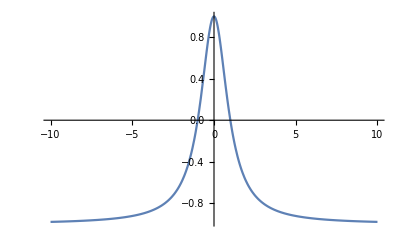

```mathematica
Plot[Cos[2*ArcTan[Abs[x]]], {x,-10,10},PlotRange->Full]
```

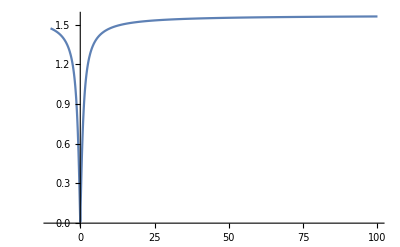

```mathematica
Plot[ArcTan[Abs[x]], {x,-10,100}, PlotRange->Full]
```

```mathematica
Manipulate[Plot[(a x^3-b x^2+c x-d x^4+e x^5)*10^-m, {x,-1,800}, PlotRange->n],{a,0,20000,.1},{b,0,100000},{c,0,2000000000},{d,0,2000,.1},{e,1,2000,.1},{n,1, 1000000000000},{m,0, 100000000}]
```

```mathematica
(10845* x^3-100000 x^2+2*10^9 x-350 x^4+x^5)*10^-10.37
```

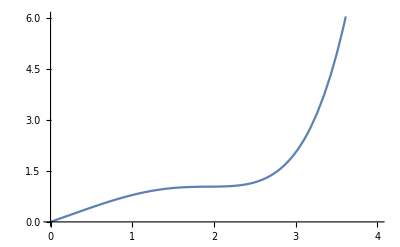

```mathematica
Plot[4.2658×10^-12 (2000000000 (100x)-100000 (100x)^2+10845 (100x)^3-350 (100x)^4+(100x)^5),{x,0,4}]
```

```mathematica
Plot3D[ArcTan[Abs[4.2658×10^-12.01 (2000000000 (100 √(x^2+y^2))-100000 (100 √(x^2+y^2))^2+10845 (100 √(x^2+y^2))^3-350 (100 √(x^2+y^2))^4+(100 √(x^2+y^2))^5)]],{x,-10,10},{y,-10,10}, PlotRange->Full]
```

-Graphics3D-

```mathematica
Plot3D[-Cos[2ArcTan[4.2658×10^-12.01 (2000000000 (100 √(x^2+y^2))-100000 (100 √(x^2+y^2))^2+10845 (100 √(x^2+y^2))^3-350 (100 √(x^2+y^2))^4+(100 √(x^2+y^2))^5)]],{x,-8,8},{y,-8,8}, PlotRange->Full]
```

-Graphics3D-

```mathematica
f[x_,y_] := 2ArcTan[4.2658×10^-12.01 (2000000000 (100 √(x^2+y^2))-100000 (100 √(x^2+y^2))^2+10845 (100 √(x^2+y^2))^3-350 (100 √(x^2+y^2))^4+(100 √(x^2+y^2))^5)]
X[x_,y_,z_,γ_, m_] := (Sin[f[x,y]]) Cos[m*ArcTan[x,y]+γ](UnitStep[z+0.1] UnitStep[0.1-z])
Y[x_,y_,z_, γ_, m_] := ( Sin[f[x,y]]) Sin[m*ArcTan[x,y]+γ](UnitStep[z+0.1] UnitStep[0.1-z])
Z[x_,y_,z_] :=-Cos[f[x,y]]  (UnitStep[z+0.1] UnitStep[0.1-z])
zColor[x_,y_] :=-Cos[f[x,y]] +1
```

```mathematica
Manipulate[VectorPlot3D[{X[x,y,z,γ,m],Y[x,y,z,γ,m],Z[x,y,z]},{x,-4.25,4.25},{y,-4.25,4.25},{z,-4.25,4.25},VectorColorFunction->"Rainbow", VectorStyle->"Arrow3D",ImageSize->600, VectorPoints->33], {γ, 0, 2*π,π/8},{m,-2,5,1}]
```

```mathematica
f[x_,y_] := 2ArcTan[4.2658×10^-12.01 (2000000000 (100 √(x^2+y^2))-100000 (100 √(x^2+y^2))^2+10845 (100 √(x^2+y^2))^3-350 (100 √(x^2+y^2))^4+(100 √(x^2+y^2))^5)]
X[x_,y_,z_,γ_, m_] := (Sin[f[x,y]]) Cos[m*ArcTan[x,y]+γ](UnitStep[z+0.1] UnitStep[0.1-z])
Y[x_,y_,z_, γ_, m_] := ( Sin[f[x,y]]) Sin[m*ArcTan[x,y]+γ](UnitStep[z+0.1] UnitStep[0.1-z])
Z[x_,y_,z_] :=-Cos[f[x,y]]  (UnitStep[z+0.1] UnitStep[0.1-z])
zColor[x_,y_] :=-Cos[f[x,y]] +1
```

```mathematica
Manipulate[VectorPlot3D[{X[x,y,z,γ,m],Y[x,y,z,γ,m],Z[x,y,z]},{x,-4.5,4.5},{y,-4.5,4.5},{z,-4.5,4.5},VectorColorFunction->"Rainbow", VectorStyle->"Arrow3D",ImageSize->600, VectorPoints->27], {γ, 0, 2*π,π/8},{m,-2,5}]
```

```mathematica
VectorPlot3D[{X[x,y,z,0,1]+X[x,y,z,0,-1],Y[x,y,z,0,1]+Y[x,y,z,0,-1],Z[x,y,z]+Z[x,y,z]},{x,-4.5,4.5},{y,-4.5,4.5},{z,-4.5,4.5},VectorColorFunction->"Rainbow", VectorStyle->"Arrow3D",ImageSize->600, VectorPoints->27]
```

-Graphics3D-

```mathematica
f[x_,y_] := 2ArcTan[x^2+y^2]
X[x_,y_,z_,γ_, m_] := (Sin[f[x,y]]) Cos[m*ArcTan[x,y]+γ](UnitStep[z+0.1] UnitStep[0.1-z])
Y[x_,y_,z_, γ_, m_] := ( Sin[f[x,y]]) Sin[m*ArcTan[x,y]+γ](UnitStep[z+0.1] UnitStep[0.1-z])
Z[x_,y_,z_] :=-Cos[f[x,y]]  (UnitStep[z+0.1] UnitStep[0.1-z])
```

```mathematica
Manipulate[VectorPlot3D[{1/2(X[x+d^3,y,z,π/2,1]+X[x-d^3,y,z,-π/2,1]),1/2(Y[x+d^3,y,z,π/2,1]+Y[x-d^3,y,z,-π/2,1]),0},{x,-4.5,4.5},{y,-4.5,4.5},{z,-4.5,4.5},VectorColorFunction->"Rainbow", VectorStyle->"Arrow3D",ImageSize->600, VectorPoints->27,Boxed->False,Background->None],{d,-0.1,4^(1/3)}]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["skyrmions_separating.avi"]]]
```

```mathematica
plots = Table[VectorPlot3D[{1/2(X[x+d^2,y,z,π/2,1]+X[x-d^2,y,z,-π/2,1]),1/2(Y[x+d^2,y,z,π/2,1]+Y[x-d^2,y,z,-π/2,1]),0},{x,-4.5,4.5},{y,-4.5,4.5},{z,-4.5,4.5},VectorColorFunction->"Rainbow", VectorStyle->"Arrow3D",ImageSize->600, VectorPoints->27,Boxed->False,Background->None],{d,0,4^(1/2),0.01}];
```

```mathematica
Export["skyrmions_separating.avi", plots]
```

skyrmions_separating.avi

```mathematica
.1/.005 +4^(1/3)/0.005
```

337.48

```mathematica
X[x_,y_,z_] := 0
Y[x_,y_,z_] := Sin[x](UnitStep[z+0.1] UnitStep[0.1-z])
Z[x_,y_,z_] :=Cos[x]  (UnitStep[z+0.1] UnitStep[0.1-z])
```

```mathematica
VectorPlot3D[{X[x,y,z],Y[x,y,z](UnitStep[y+0.1] UnitStep[0.1-y]),Z[x,y,z](UnitStep[y+0.1] UnitStep[0.1-y])},{x,-4.5,4.5},{y,-4.5,4.5},{z,-4.5,4.5},VectorColorFunction->"Rainbow", VectorStyle->"Arrow3D",ImageSize->600, VectorPoints->27,Boxed->False,Background->None]
```

-Graphics3D-

```mathematica
X[x_,y_,z_] := 0
Y[x_,y_,z_] := Abs[Sin[x]](UnitStep[z+0.1] UnitStep[0.1-z])
Z[x_,y_,z_] := Cos[ x] (UnitStep[z+0.1] UnitStep[0.1-z])
```

```mathematica
VectorPlot3D[{X[2x,y,z],Y[2x,y,z](UnitStep[y+0.1] UnitStep[0.1-y]),Z[2x,y,z](UnitStep[y+0.1] UnitStep[0.1-y])},{x,-4.5,4.5},{y,-4.5,4.5},{z,-4.5,4.5},VectorColorFunction->"Rainbow", VectorStyle->"Arrow3D",ImageSize->600, VectorPoints->27,Boxed->False,Background->None]
```

-Graphics3D-

```mathematica
M = {0, Sin[x], Cos[x]}

Curl[M,{x,y,z}]
```

{0,Sin[x],Cos[x]}

{0,Sin[x],Cos[x]}

```mathematica
Integrate[Sin[x]/Sqrt[a+(y-x)^2],{x,-Infinity, Infinity}, Assumptions->a>0]
```

```mathematica
Integrate[Sin[x]/(√(a+(-x+y)^2)),{x,-∞,∞},Assumptions->a>0&&y∈Reals]
```

```mathematica
Integrate[1/(√(a+(-x+y)^2)),{x,-∞,∞},Assumptions->a>0&&y∈Reals]
```

Integrate::idiv: Integral of 1/√a + (-x + y)^2 does not converge on {-∞, ∞}.

```mathematica
Integrate[1/(√(a+(-x+y)^2)),{x,-d,d},Assumptions->{a,d}>0&&{y,x}∈Reals]
```

Log[-(d+√(a+(d-y)^2)-y)/(d+y-√(a+(d+y)^2))]

```mathematica
Integrate[Log[-(√(a+(d/2-y)^2+(z-x)^2)-y+d/2)/(d/2+y-√(a+(d/2+y)^2+(z-x)^2))],{x,-T/2,T/2},Assumptions->{a,d,T}>0&&{y,x}∈Reals]
```

Integrate[Log[-(d/2-y+√(a+(d/2-y)^2+(-x+z)^2))/(d/2+y-√(a+(d/2+y)^2+(-x+z)^2))],{x,-T/2,T/2},Assumptions→{a,d,T}>0&&(y|x)∈Reals]

```mathematica
FourierTransform[Sqrt[Sin[q*x]^2], x, k, Assumptions->q>0]
```

FourierTransform[√(Sin[q x]^2),x,k,Assumptions→q>0]

```mathematica
FourierTransform[Cos[q x],x,k]
```

√(π/2) DiracDelta[k-q]+√(π/2) DiracDelta[k+q]

```mathematica
2/(2π)^(3/2)FullSimplify[InverseFourierTransform[((DiracDelta[k-q]-DiracDelta[k+q])k)/Sqrt[k^2],k,x, Assumptions->q>0]]
```

Cos[q x]/π^2

```mathematica
TrigToExp[Cos[q x]/π^2]
```

ⅇ^(-ⅈ q x)/(2 π^2)+ⅇ^(ⅈ q x)/(2 π^2)

```mathematica
FullSimplify[(ⅇ^(-ⅈ q x) (1+ⅇ^(2 ⅈ q x)) q)/(√(2 π) Abs[q])]
```

√(2/π) Cos[q x] Sign[q]

```mathematica
FullSimplify[(ⅇ^(-ⅈ k q) q)/(√(2 π) Abs[q])]
```

(ⅇ^(-ⅈ k q) Sign[q])/(√(2 π))

```mathematica
Integrate[(DiracDelta[k+x]),{k,-Infinity, Infinity}]
```

ConditionalExpression[1,x∈Reals]

```mathematica
Integrate[Exp[-I*k*z],{z,-T/2, T/2}, Assumptions->{T,k}∈Reals]
```

(2 Sin[(k T)/2])/k

```mathematica
X[x_,y_,z_] := 0
Y[x_,y_,z_] := Sin[x](UnitStep[z+0.1] UnitStep[0.1-z])
Z[x_,y_,z_] := Cos[ x] (UnitStep[z+0.1] UnitStep[0.1-z])
zColor[x_,y_] :=Cos[x]
```

```mathematica
VectorPlot3D[{X[2x,2y,z],Y[2x,2y,z],Z[2x,2y,z]},{x,0,10},{y,0,10},{z,0,10},VectorColorFunction->Function[{x,y, z},ColorData["Rainbow"][Z[ 2x,2y,z]]], VectorStyle->"Arrow3D",ImageSize->600, VectorPoints->27,Boxed->False,Background->None]
```

-Graphics3D-

```mathematica
FullSimplify[Sin[2*ArcTan[ρ]]-2 ρ/(1+ρ^2)]
```

0

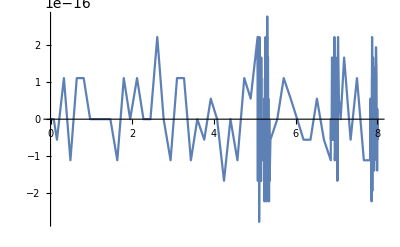

```mathematica
Plot[-(2 ρ)/(1+ρ^2)+Sin[2 ArcTan[ρ]],{ρ,0,8}]
```

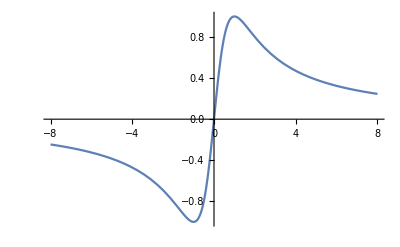

```mathematica
Plot[Sin[2 ArcTan[ρ]],{ρ,-8,8}]
```

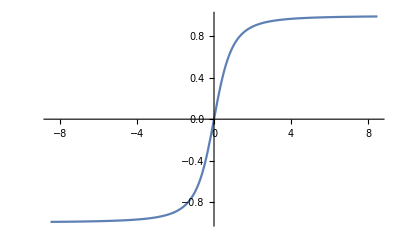

```mathematica
Plot[ρ/(√(1+ρ^2)),{ρ,-8.493333333333334,8.493333333333334}]
```

```mathematica
Cos[ArcTan[ρ]]
```

1/(√(1+ρ^2))

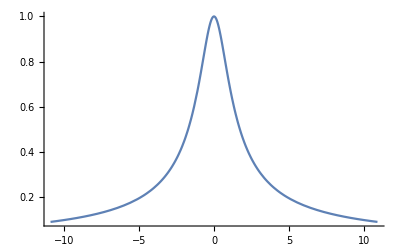

```mathematica
Plot[1/(√(1+ρ^2)),{ρ,-10.92,10.92}]
```

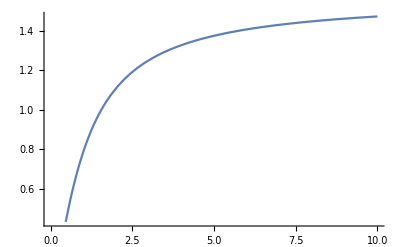

```mathematica
Plot[ArcTan[ρ],{ρ,0,10}]
```

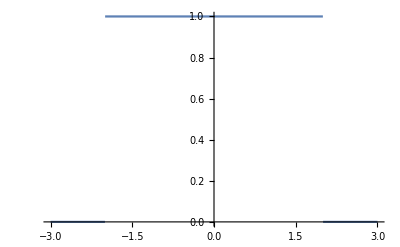

```mathematica
Plot[HeavisideTheta[2+z]HeavisideTheta[2-z], {z,-3,3}]
```

```mathematica
1/(√(2π))Integrate[Exp[I kz z], {z,-t/2,t/2}, Assumptions->kz∈Reals]
```

ConditionalExpression[(√(2/π) Sin[(kz t)/2])/kz,t∈Reals]

```mathematica
FourierTransform[(1-x^2+y^2)/(1+x^2+y^2),{x,y},{kx,kz}]
```

FourierTransform[(1-x^2+y^2)/(1+x^2+y^2),{x,y},{kx,kz}]

```mathematica
Integrate[-BesselJ[0, k ρ]ρ,{ρ,0,Infinity}, Assumptions->{k,ρ}∈Reals]
```

Integrate[-ρ BesselJ[0,k ρ],{ρ,0,∞},Assumptions→(k|ρ)∈Reals]

```mathematica
D[BesselJ[0,k ρ],k]
```

-ρ BesselJ[1,k ρ]

```mathematica
FullSimplify[(1-x^2)/(1+x^2)]
```

-1+2/(1+x^2)

```mathematica
Integrate[Cos[m ϕ +γ]Exp[I ρ(kx Cos[ϕ]+ky Sin[ϕ])], {ϕ,0,2π}, Assumptions->{kx,ky,γ}∈Reals&&ρ≥0]
```

Integrate[ⅇ^(ⅈ ρ (6 kx Cos[ϕ]+ky Sin[ϕ])) Cos[γ+m ϕ],{ϕ,0,2 π},Assumptions→(kx|ky|γ)∈Reals&&ρ≥0]

```mathematica
Integrate[Cos[m ϕ ]Exp[I ρ(kx Cos[ϕ]+ky Sin[ϕ])], {ϕ,0,2π}, Assumptions->{kx,ky,γ}∈Reals&&ρ≥0]
```

Integrate[ⅇ^(ⅈ ρ (6 kx Cos[ϕ]+ky Sin[ϕ])) Cos[m ϕ],{ϕ,0,2 π},Assumptions→(kx|ky|γ)∈Reals&&ρ≥0]

```mathematica
Integrate[Cos[ϕ +γ]Exp[I ρ k Cos[ϕ]], {ϕ,0,2π}, Assumptions->{k,γ}∈Reals&&ρ≥0]
```

2 ⅈ π BesselJ[1,k ρ] Cos[γ]

```mathematica
Integrate[Cos[ϕ +γ]Exp[I ρ k Cos[ϕ+ϕk]], {ϕ,0,2π}, Assumptions->{k,γ,ϕk}∈Reals&&ρ≥0]
```

2 ⅈ π BesselJ[1,k ρ] Cos[γ-ϕk]

```mathematica
Integrate[(BesselJ[1,k ρ] ρ^2)/(1+ρ^2), {ρ, 0, Infinity}, Assumptions->k∈Reals]
```

ConditionalExpression[BesselK[1,k],k>0]

```mathematica
Integrate[ρ^2/(1+ρ^2), {ρ, 0, Infinity}, Assumptions->k∈Reals]
```

Integrate[ρ^2/(1+ρ^2),{ρ,0,∞},Assumptions→k∈Reals]

```mathematica
Integrate[ BesselJ[1,k ρ],{ρ,0,Infinity},Assumptions->k∈Reals]
```

1/k

```mathematica
-Integrate[ BesselJ[1,k ρ]/(1+ρ^2),{ρ,0,Infinity},Assumptions->k∈Reals]
```

ConditionalExpression[-1/k+BesselK[1,k],k>0]

```mathematica
Integrate[Sin[ϕ +γ]Exp[I ρ k Cos[ϕ+ϕk]], {ϕ,0,2π}, Assumptions->{k,γ,ϕk}∈Reals&&ρ≥0]
```

2 ⅈ π BesselJ[1,k ρ] Sin[γ-ϕk]

```mathematica
Integrate[(BesselJ[1,k ρ] ρ^2)/(1+ρ^2), {ρ, 0, Infinity}, Assumptions->k∈Reals]
```

ConditionalExpression[BesselK[1,k],k>0]

```mathematica
InverseFourierTransform[Sin[(kz t)/2]/(kz (kz^2+k^2)), kz, z, Assumptions->t>0&&k>0]
```

```mathematica
InverseFourierTransform[Sin[(kz t)/2]/(kz (k^2)), kz, z, Assumptions->t>0&&k>0]
```

(1/2 √(π/2) Sign[t-2 z]+1/2 √(π/2) Sign[t/2+z])/k^2

```mathematica
InverseFourierTransform[(kz Sin[(kz t)/2])/(k^2 (kz^2+k^2)), kz, z, Assumptions->t>0&&k>0]
```

(ⅇ^((k t)/2-k z) √(π/2) DiracDelta[t-2 z])/k^3-(ⅇ^(-(k t)/2+k z) √(π/2) DiracDelta[t-2 z])/k^3-(ⅇ^(-(k t)/2-k z) √(π/2) DiracDelta[t+2 z])/k^3+(ⅇ^((k t)/2+k z) √(π/2) DiracDelta[t+2 z])/k^3-(ⅇ^((k t)/2+k z) √(π/2) HeavisideTheta[-t/2-z])/(2 k^2)+(ⅇ^(-(k t)/2+k z) √(π/2) HeavisideTheta[t/2-z])/(2 k^2)-(ⅇ^((k t)/2-k z) √(π/2) HeavisideTheta[-t/2+z])/(2 k^2)+(ⅇ^(-(k t)/2-k z) √(π/2) HeavisideTheta[t/2+z])/(2 k^2)

```mathematica
Plot[1/2(Sign[4-2 z]+ Sign[4/2+z]), {z,-3,3}]
```

-Graphics-

```mathematica
Plot[HeavisideTheta[2+z]HeavisideTheta[2-z], {z,-3,3}]
```

-Graphics-

```mathematica
FullSimplify[(√(π/2) HeavisideTheta[t/2+z]HeavisideTheta[t/2-z])/k^2-((ⅇ^((k t)/2-k z) √(π/2) DiracDelta[t-2 z])/k^3-(ⅇ^(-(k t)/2+k z) √(π/2) DiracDelta[t-2 z])/k^3-(ⅇ^(-(k t)/2-k z) √(π/2) DiracDelta[t+2 z])/k^3+(ⅇ^((k t)/2+k z) √(π/2) DiracDelta[t+2 z])/k^3-(ⅇ^((k t)/2+k z) √(π/2) HeavisideTheta[-t/2-z])/(2 k^2)+(ⅇ^(-(k t)/2+k z) √(π/2) HeavisideTheta[t/2-z])/(2 k^2)-(ⅇ^((k t)/2-k z) √(π/2) HeavisideTheta[-t/2+z])/(2 k^2)+(ⅇ^(-(k t)/2-k z) √(π/2) HeavisideTheta[t/2+z])/(2 k^2)), Assumptions->{k,t,z}∈Reals]
```

-(ⅇ^(1/2 k (t-2 z)) √(π/2) DiracDelta[t-2 z])/k^3+(ⅇ^(k (-t/2+z)) √(π/2) DiracDelta[t-2 z])/k^3+(ⅇ^(-1/2 k (t+2 z)) √(π/2) DiracDelta[t+2 z])/k^3-(ⅇ^((k t)/2+k z) √(π/2) DiracDelta[t+2 z])/k^3+1/(2 k^2)ⅇ^(-1/2 k (t+2 z)) √(π/2) (ⅇ^(k t) (ⅇ^(2 k z) HeavisideTheta[-t/2-z]+HeavisideTheta[-t/2+z])-HeavisideTheta[t/2+z]-ⅇ^(k z) HeavisideTheta[t-2 z] (ⅇ^(k z)-2 ⅇ^((k t)/2) HeavisideTheta[t/2+z]))

```mathematica
-(ⅇ^(1/2 k (t-2 z)) √(π/2) DiracDelta[t-2 z])/k^3+(ⅇ^(k (-t/2+z)) √(π/2) DiracDelta[t-2 z])/k^3+(ⅇ^(-1/2 k (t+2 z)) √(π/2) DiracDelta[t+2 z])/k^3-(ⅇ^((k t)/2+k z) √(π/2) DiracDelta[t+2 z])/k^3+1/(2 k^2)ⅇ^(-1/2 k (t+2 z)) √(π/2) (-ⅇ^(2 k z) HeavisideTheta[t-2 z]+ⅇ^(k (t+2 z)) HeavisideTheta[-t/2-z]+ⅇ^(k t) HeavisideTheta[-t/2+z]-HeavisideTheta[t/2+z]+ⅇ^((k t)/2+k z) (HeavisideTheta[t/2+z]HeavisideTheta[t/2-z]))
```

-(ⅇ^(1/2 k (t-2 z)) √(π/2) DiracDelta[t-2 z])/k^3+(ⅇ^(k (-t/2+z)) √(π/2) DiracDelta[t-2 z])/k^3+(ⅇ^(-1/2 k (t+2 z)) √(π/2) DiracDelta[t+2 z])/k^3-(ⅇ^((k t)/2+k z) √(π/2) DiracDelta[t+2 z])/k^3+1/(2 k^2)ⅇ^(-1/2 k (t+2 z)) √(π/2) (-ⅇ^(2 k z) HeavisideTheta[t-2 z]+ⅇ^(k (t+2 z)) HeavisideTheta[-t/2-z]+ⅇ^(k t) HeavisideTheta[-t/2+z]-HeavisideTheta[t/2+z]+ⅇ^((k t)/2+k z) HeavisideTheta[t/2-z] HeavisideTheta[t/2+z])

```mathematica
Simplify[1/(2 k^2)ⅇ^(-1/2 k (t+2 z)) √(π/2) (ⅇ^(2 k z) HeavisideTheta[t-2 z]-ⅇ^(k t) (ⅇ^(2 k z) HeavisideTheta[-t/2-z]+HeavisideTheta[-t/2+z])+HeavisideTheta[t/2+z]), Assumptions->{k,t,z}∈Reals]
```

1/(2 k^2)ⅇ^(-1/2 k (t+2 z)) √(π/2) (ⅇ^(2 k z) HeavisideTheta[t-2 z]-ⅇ^(k t) (ⅇ^(2 k z) HeavisideTheta[-t/2-z]+HeavisideTheta[-t/2+z])+HeavisideTheta[t/2+z])

```mathematica
Manipulate[Plot[1/(2 k^2)ⅇ^(-1/2 k (t+2 z)) √(π/2) (ⅇ^(2 k z) HeavisideTheta[t-2 z]-ⅇ^(k t) (ⅇ^(2 k z) HeavisideTheta[-t/2-z]+HeavisideTheta[-t/2+z])+HeavisideTheta[t/2+z]),{t,-8,8}],{k,-8,8},{z,-2,2}]
```

```mathematica
D[HeavisideTheta[2+z]HeavisideTheta[2-z],z]
```

DiracDelta[2+z] HeavisideTheta[2-z]-DiracDelta[-2+z] HeavisideTheta[2+z]

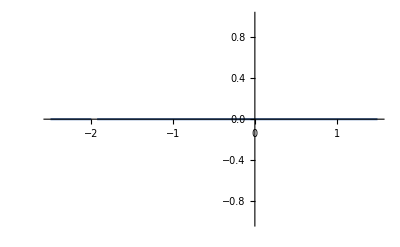

```mathematica
Plot[DiracDelta[2+z] HeavisideTheta[2-z]-DiracDelta[-2+z] HeavisideTheta[2+z], {z,-2.5,1.5}]
```

```mathematica
Integrate[1/(√(ξ^2+(z-ζ)^2)), {ζ,-t,t}, Assumptions->{ξ,z}∈Reals&&t>0]
```

ConditionalExpression[Log[(t+z+√((t+z)^2+ξ^2))/(-t+z+√((t-z)^2+ξ^2))],ξ≠0||t<z||t+z<0]

```mathematica
Limit[2*π R*Log[(t+z+√((t+z)^2+R^2+ρ^2-2R ρ Cos[ϕ-θ]))/(-t+z+√((t-z)^2+R^2+ρ^2-2R ρ Cos[ϕ-θ]))],R->Infinity]
```

4 π t

```mathematica
Integrate[x^2/((x^2+1)^2 √(x^2+ρ^2-ρ x b+z^2)), {x,0,Infinity}, Assumptions->{ρ,x}>0&&Abs[b]≤1&&z∈Reals]
```

ConditionalExpression[1/8 (-(4 b ρ √(z^2+ρ^2))/(1-2 z^2+z^4-2 ρ^2+b^2 ρ^2+2 z^2 ρ^2+ρ^4)+((2 z^2+ⅈ b ρ+2 ρ^2) Log[(8 √(1-z^2-ⅈ b ρ-ρ^2) (2 ⅈ z^2-b ρ+2 ⅈ ρ^2+2 √(1-z^2-ⅈ b ρ-ρ^2) √(z^2+ρ^2)))/(2 z^2+ⅈ b ρ+2 ρ^2)])/((1-z^2-ⅈ b ρ-ρ^2)^(3/2))-((2 z^2-ⅈ b ρ+2 ρ^2) Log[(8 √(1-z^2+ⅈ b ρ-ρ^2) (2 ⅈ z^2+b ρ+2 ⅈ ρ^2+2 √(1-z^2+ⅈ b ρ-ρ^2) √(z^2+ρ^2)))/(2 z^2-ⅈ b ρ+2 ρ^2)])/((1-z^2+ⅈ b ρ-ρ^2)^(3/2)))+1/8 (-(4 (-1+z^2+ρ^2))/(1+z^4+(-2+b^2) ρ^2+ρ^4+2 z^2 (-1+ρ^2))-((2 z^2+ρ (ⅈ b+2 ρ)) Log[(8 √(1-z^2-ⅈ b ρ-ρ^2) (b ρ+2 ⅈ (1+√(1-z^2-ⅈ b ρ-ρ^2))))/(2 z^2+ρ (ⅈ b+2 ρ))])/((1-z^2-ⅈ b ρ-ρ^2)^(3/2))+((2 z^2+ρ (-ⅈ b+2 ρ)) Log[(8 √(1-z^2+ⅈ b ρ-ρ^2) (-b ρ-2 ⅈ (-1+√(1-z^2+ⅈ b ρ-ρ^2))))/(2 z^2+ρ (-ⅈ b+2 ρ))])/((1-z^2+ⅈ b ρ-ρ^2)^(3/2))),(Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0||Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0)&&((z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Im[b]>0&&Abs[b]≤1&&Im[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Im[b]≥-1&&Im[b]<0&&Im[b]≥-1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Im[b]>0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Im[b]>0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Im[b]>0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Im[b]<0&&Im[b]≥-1&&Abs[b]≤1&&Im[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&b≥-1&&b≤1&&Abs[b]≤1&&Im[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Im[b]≥-1&&Im[b]>0&&Im[b]<0&&Abs[b]≤1&&Im[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Im[b]≥-1&&Im[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Im[b]≥-1&&Abs[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Im[b]≥-1&&Im[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Im[b]≥-1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Im[b]≥-1&&Im[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Im[b]≥-1&&Abs[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Im[b]≥-1&&Im[b]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&b≥-1&&Re[b]≥-1&&b≥-1&&b≤1&&Abs[b]≤1&&Re[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Im[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Im[b]≥-1&&Abs[b]≤1&&Im[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Im[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Im[b]≥-1&&Abs[b]≤1&&Im[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Im[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Im[b]≥-1&&Abs[b]≤1&&Im[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Im[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Im[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Im[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Im[b]≥-1&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Im[b]≥-1&&Im[b]>0&&Im[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Im[b]≥-1&&Im[b]>0&&Im[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Im[b]≥-1&&Im[b]>0&&Im[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Im[b]≥-1&&Re[b]>0&&Im[b]<0&&Re[b]<1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Im[b]≥-1&&Im[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Im[b]≥-1&&Im[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Im[b]≥-1&&Im[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&Abs[b]≤1&&Im[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&Im[b]<0&&Re[b]<1&&Abs[b]≤1&&Im[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Im[b]≥-1&&Re[b]>-1&&Im[b]>0&&Im[b]<0&&Re[b]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Im[b]≥-1&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Im[b]≥-1&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Im[b]≥-1&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Im[b]≥-1&&Im[b]>0&&Re[b]>0&&Im[b]<0&&Re[b]<1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Im[b]≥-1&&Re[b]>0&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Im[b]≥-1&&Re[b]>0&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Im[b]≥-1&&Re[b]>0&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Re[b]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Re[b]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Re[b]<1&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Re[b]<1&&b≥-1&&b≤1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]<0&&Re[b]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]<0&&Re[b]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]<0&&Re[b]<1&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]<0&&Re[b]<1&&b≥-1&&b≤1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Im[b]≥-1&&Abs[b]≤1&&Re[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]<0&&Im[b]≥-1&&Abs[b]≤1&&Re[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]≥-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]<0&&Re[b]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Im[b]≥-1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]≥-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]<0&&Re[b]<0&&Im[b]≥-1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&b≥-1&&Re[b]≥-1&&Im[b]>0&&b≤1&&Abs[b]≤1&&Im[b]≤1&&Re[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&b≥-1&&Re[b]≥-1&&Im[b]<0&&Im[b]≥-1&&b≤1&&Abs[b]≤1&&Re[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Re[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Re[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]≥-1&&√(1-Im[b]^2)+Re[b]≥0&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]≥-1&&√(1-Im[b]^2)+Re[b]≥0&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]≥-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]<0&&Re[b]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]≥-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]<0&&Re[b]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]<1&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Re[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]<1&&b≥-1&&b≤1&&Abs[b]≤1&&Re[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]≥-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]<1&&Re[b]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]≥-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]<1&&Re[b]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]<0&&Re[b]<0&&Im[b]≥-1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]<0&&Re[b]<1&&Im[b]≥-1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]<0&&Re[b]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Im[b]≥-1&&b≤1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]<0&&Re[b]<0&&Im[b]≥-1&&b≤1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]<0&&Re[b]<1&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Im[b]≥-1&&b≤1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]<0&&Re[b]<1&&Im[b]≥-1&&b≤1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Im[b]≥-1&&Re[b]>-1&&Im[b]>0&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Im[b]≥-1&&Re[b]>-1&&Im[b]>0&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Im[b]≥-1&&Re[b]>-1&&Im[b]>0&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Im[b]≥-1&&Im[b]>0&&Re[b]>0&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Im[b]≥-1&&Im[b]>0&&Re[b]>0&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Im[b]≥-1&&Im[b]>0&&Re[b]>0&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]<0&&Re[b]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>0&&Im[b]<0&&Re[b]<1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]<0&&Re[b]<1&&b≥-1&&b≤1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&√(1-Re[b]^2)≥Im[b]&&Im[b]<1&&Re[b]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&√(1-Re[b]^2)≥Im[b]&&Im[b]<1&&Re[b]<1&&b≥-1&&b≤1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&b≤1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>0&&Im[b]<0&&Re[b]<1&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>0&&Im[b]<0&&Re[b]<1&&b≤1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]>0&&Im[b]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤1&&Re[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]>0&&Im[b]<0&&Abs[b]≤1&&Im[b]≤1&&Re[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]≥-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]>0&&Im[b]<0&&Re[b]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]≥-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]>0&&Im[b]<0&&Re[b]<0&&Abs[b]≤1&&Im[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]>0&&Im[b]<1&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤1&&Re[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]<0&&Im[b]<1&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Im[b]≥-1&&Abs[b]≤1&&Re[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]<0&&Im[b]<1&&Im[b]≥-1&&Abs[b]≤1&&Re[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]≥-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]>0&&Im[b]<1&&Re[b]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]≥-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]<0&&Im[b]<1&&Re[b]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Im[b]≥-1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]≥-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]<0&&Im[b]<1&&Re[b]<0&&Im[b]≥-1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Re[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&Abs[b]≤1&&Re[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Re[b]>0&&Im[b]<0&&Re[b]<1&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Re[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Re[b]>0&&Im[b]<0&&Re[b]<1&&Abs[b]≤1&&Re[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]≥-1&&√(1-Im[b]^2)+Re[b]≥0&&Re[b]>-1&&Im[b]>0&&Im[b]<0&&Re[b]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]≥-1&&√(1-Im[b]^2)+Re[b]≥0&&Re[b]>-1&&Im[b]>0&&Im[b]<0&&Re[b]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]≥-1&&√(1-Im[b]^2)+Re[b]≥0&&Re[b]>0&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]≥-1&&√(1-Im[b]^2)+Re[b]≥0&&Re[b]>0&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]≥-1&&√(1-Im[b]^2)+Re[b]≥0&&Re[b]>-1&&Im[b]>0&&Im[b]<1&&Re[b]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]≥-1&&√(1-Im[b]^2)+Re[b]≥0&&Re[b]>-1&&Im[b]>0&&Im[b]<1&&Re[b]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]≥-1&&√(1-Im[b]^2)+Re[b]≥0&&Re[b]>-1&&Im[b]<0&&Im[b]<1&&Re[b]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]≥-1&&√(1-Im[b]^2)+Re[b]≥0&&Re[b]>-1&&Im[b]<0&&Im[b]<1&&Re[b]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&b≥-1&&Re[b]≥-1&&Re[b]>-1&&Im[b]>0&&Re[b]<0&&b≤1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&b≥-1&&Re[b]≥-1&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&b≤1&&Abs[b]≤1&&Re[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&b≥-1&&Re[b]≥-1&&Im[b]>0&&Re[b]>0&&Re[b]<1&&b≤1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&b≥-1&&Re[b]≥-1&&Re[b]>0&&Im[b]<0&&Re[b]<1&&b≤1&&Abs[b]≤1&&Re[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]>0&&Im[b]<0&&Re[b]<0&&Abs[b]≤1&&Im[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Im[b]≥-1&&Abs[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Im[b]≥-1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Im[b]≥-1&&Abs[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]>0&&Im[b]<0&&Re[b]<1&&Abs[b]≤1&&Im[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Im[b]≥-1&&Abs[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Im[b]≥-1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Im[b]≥-1&&Abs[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Im[b]>0&&Re[b]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&Im[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Im[b]<0&&Re[b]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Im[b]≥-1&&b≤1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Im[b]<0&&Re[b]<0&&Im[b]≥-1&&b≤1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&√(1-Re[b]^2)≥Im[b]&&Im[b]<0&&Im[b]<1&&Re[b]<0&&Im[b]≥-1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Im[b]>0&&Re[b]<1&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&Im[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Im[b]<0&&Re[b]<1&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Im[b]≥-1&&b≤1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Im[b]<0&&Re[b]<1&&Im[b]≥-1&&b≤1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&√(1-Re[b]^2)≥Im[b]&&Im[b]<0&&Im[b]<1&&Re[b]<1&&Im[b]≥-1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]>0&&Im[b]<0&&Re[b]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&Im[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]>0&&Im[b]<0&&Re[b]<0&&b≤1&&Abs[b]≤1&&Im[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Im[b]≥-1&&b≤1&&Abs[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Im[b]≥-1&&b≤1&&Abs[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]>0&&Im[b]<0&&Re[b]<1&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&Im[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]>0&&Im[b]<0&&Re[b]<1&&b≤1&&Abs[b]≤1&&Im[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Im[b]≥-1&&b≤1&&Abs[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Im[b]≥-1&&b≤1&&Abs[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>-1&&Im[b]>0&&Im[b]<0&&Re[b]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>0&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]>0&&Re[b]>0&&Im[b]<0&&Re[b]<1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>0&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>0&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>0&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Re[b]>-1&&Im[b]>0&&Re[b]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Re[b]>-1&&Im[b]>0&&Re[b]<0&&b≤1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&b≤1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&√(1-Re[b]^2)≥Im[b]&&Re[b]>-1&&Im[b]>0&&Im[b]<1&&Re[b]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&√(1-Re[b]^2)≥Im[b]&&Re[b]>-1&&Im[b]<0&&Im[b]<1&&Re[b]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&√(1-Re[b]^2)≥Im[b]&&Im[b]<1&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&√(1-Re[b]^2)≥Im[b]&&Im[b]<1&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&√(1-Re[b]^2)≥Im[b]&&Im[b]<1&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Im[b]>0&&Re[b]>0&&Re[b]<1&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Im[b]>0&&Re[b]>0&&Re[b]<1&&b≤1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Re[b]>0&&Im[b]<0&&Re[b]<1&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Re[b]>0&&Im[b]<0&&Re[b]<1&&b≤1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&√(1-Re[b]^2)≥Im[b]&&Im[b]>0&&Re[b]>0&&Im[b]<1&&Re[b]<1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&√(1-Re[b]^2)≥Im[b]&&Re[b]>0&&Im[b]<0&&Im[b]<1&&Re[b]<1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&√(1-Re[b]^2)≥Im[b]&&Im[b]<1&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&√(1-Re[b]^2)≥Im[b]&&Im[b]<1&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&√(1-Re[b]^2)≥Im[b]&&Im[b]<1&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≥-1&&b≤1&&Abs[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>-1&&Im[b]>0&&Im[b]<0&&Re[b]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>-1&&Im[b]>0&&Im[b]<0&&Re[b]<0&&b≤1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>0&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>0&&Im[b]<0&&Re[b]<0&&Re[b]<1&&b≤1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&Re[b]<1&&b≤1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]>0&&Re[b]>0&&Im[b]<0&&Re[b]<1&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]>0&&Re[b]>0&&Im[b]<0&&Re[b]<1&&b≤1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>0&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>0&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Re[b]>-1&&Im[b]>0&&Im[b]<0&&Re[b]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Re[b]>-1&&Im[b]>0&&Im[b]<0&&Re[b]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]>0&&Re[b]>0&&Im[b]<0&&Re[b]<1&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]>0&&Re[b]>0&&Im[b]<0&&Re[b]<1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]≥-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]>0&&Re[b]>0&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]≥-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]>0&&Re[b]>0&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Re[b]>-1&&Im[b]>0&&Im[b]<1&&Re[b]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Re[b]>-1&&Im[b]>0&&Im[b]<1&&Re[b]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Re[b]>-1&&Im[b]<0&&Im[b]<1&&Re[b]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Re[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Re[b]>-1&&Im[b]<0&&Im[b]<1&&Re[b]<0&&Abs[b]≤1&&Re[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]>0&&Re[b]>0&&Im[b]<1&&Re[b]<1&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]>0&&Re[b]>0&&Im[b]<1&&Re[b]<1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Re[b]>0&&Im[b]<0&&Im[b]<1&&Re[b]<1&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Re[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Re[b]>0&&Im[b]<0&&Im[b]<1&&Re[b]<1&&Abs[b]≤1&&Re[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]≥-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]>0&&Re[b]>0&&Im[b]<1&&Re[b]<0&&Re[b]<1&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]≥-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]>0&&Re[b]>0&&Im[b]<1&&Re[b]<0&&Re[b]<1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]≥-1&&√(1-Im[b]^2)+Re[b]≥0&&Re[b]>0&&Im[b]<0&&Im[b]<1&&Re[b]<0&&Re[b]<1&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(b∈Reals&&z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]≥-1&&√(1-Im[b]^2)+Re[b]≥0&&Re[b]>0&&Im[b]<0&&Im[b]<1&&Re[b]<0&&Re[b]<1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]>0&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]>0&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]>0&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]>0&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]>0&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]>0&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Im[b]≥-1&&b≤1&&Abs[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Im[b]≥-1&&b≤1&&Abs[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&√(1-Re[b]^2)≥Im[b]&&Im[b]<0&&Im[b]<1&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Im[b]≥-1&&Abs[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&√(1-Re[b]^2)≥Im[b]&&Im[b]<0&&Im[b]<1&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Im[b]≥-1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&√(1-Re[b]^2)≥Im[b]&&Im[b]<0&&Im[b]<1&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Im[b]≥-1&&Abs[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Im[b]≥-1&&b≤1&&Abs[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Im[b]≥-1&&b≤1&&Abs[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&√(1-Re[b]^2)≥Im[b]&&Im[b]<0&&Im[b]<1&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Im[b]≥-1&&Abs[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&√(1-Re[b]^2)≥Im[b]&&Im[b]<0&&Im[b]<1&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Im[b]≥-1&&Abs[b]≤1&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&√(1-Re[b]^2)≥Im[b]&&Im[b]<0&&Im[b]<1&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Im[b]≥-1&&Abs[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]>0&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&Im[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]>0&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&Im[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]>0&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&Im[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&Re[b]==0&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]>0&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&Im[b]≤1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>-1&&Im[b]>0&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>-1&&Im[b]>0&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>-1&&Im[b]>0&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]>0&&Re[b]>0&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>0&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>0&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>0&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>-1&&Im[b]>0&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]>0&&Re[b]>0&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]>0&&Re[b]>0&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]>0&&Re[b]>0&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Re[b]>-1&&Im[b]>0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Re[b]>-1&&Im[b]>0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Im[b]>0&&Re[b]>0&&Re[b]<0&&Re[b]<1&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Im[b]>0&&Re[b]>0&&Re[b]<0&&Re[b]<1&&b≤1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Re[b]>0&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Re[b]>0&&Im[b]<0&&Re[b]<0&&Re[b]<1&&b≤1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&√(1-Re[b]^2)≥Im[b]&&Re[b]>-1&&Im[b]>0&&Im[b]<1&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&√(1-Re[b]^2)≥Im[b]&&Re[b]>-1&&Im[b]>0&&Im[b]<1&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&√(1-Re[b]^2)≥Im[b]&&Re[b]>-1&&Im[b]>0&&Im[b]<1&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&√(1-Re[b]^2)≥Im[b]&&Re[b]>-1&&Im[b]<0&&Im[b]<1&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&√(1-Re[b]^2)≥Im[b]&&Re[b]>-1&&Im[b]<0&&Im[b]<1&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&√(1-Re[b]^2)≥Im[b]&&Re[b]>-1&&Im[b]<0&&Im[b]<1&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&√(1-Re[b]^2)≥Im[b]&&Im[b]>0&&Re[b]>0&&Im[b]<1&&Re[b]<0&&Re[b]<1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&√(1-Re[b]^2)≥Im[b]&&Re[b]>0&&Im[b]<0&&Im[b]<1&&Re[b]<0&&Re[b]<1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Re[b]>-1&&Im[b]>0&&Re[b]<0&&Re[b]<1&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Re[b]>-1&&Im[b]>0&&Re[b]<0&&Re[b]<1&&b≤1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&Re[b]<1&&b≤1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Im[b]>0&&Re[b]>0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Im[b]>0&&Re[b]>0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Re[b]>0&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Re[b]>0&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&√(1-Re[b]^2)≥Im[b]&&Re[b]>-1&&Im[b]>0&&Im[b]<1&&Re[b]<0&&Re[b]<1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&√(1-Re[b]^2)≥Im[b]&&Re[b]>-1&&Im[b]<0&&Im[b]<1&&Re[b]<0&&Re[b]<1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&√(1-Re[b]^2)≥Im[b]&&Im[b]>0&&Re[b]>0&&Im[b]<1&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&√(1-Re[b]^2)≥Im[b]&&Im[b]>0&&Re[b]>0&&Im[b]<1&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&√(1-Re[b]^2)≥Im[b]&&Im[b]>0&&Re[b]>0&&Im[b]<1&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&√(1-Re[b]^2)≥Im[b]&&Re[b]>0&&Im[b]<0&&Im[b]<1&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&√(1-Re[b]^2)≥Im[b]&&Re[b]>0&&Im[b]<0&&Im[b]<1&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&√(1-Re[b]^2)≥Im[b]&&Re[b]>0&&Im[b]<0&&Im[b]<1&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>-1&&Im[b]>0&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>-1&&Im[b]>0&&Im[b]<0&&Re[b]<0&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]>0&&Re[b]>0&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]>0&&Re[b]>0&&Im[b]<0&&Re[b]<0&&Re[b]<1&&b≤1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>0&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>0&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>-1&&Im[b]>0&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>-1&&Im[b]>0&&Im[b]<0&&Re[b]<0&&Re[b]<1&&b≤1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]>0&&Re[b]>0&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]>0&&Re[b]>0&&Im[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]>0&&Re[b]>0&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]>0&&Re[b]>0&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]>0&&Re[b]>0&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>-1&&Im[b]>0&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>-1&&Im[b]>0&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>-1&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>-1&&Im[b]>0&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Im[b]>0&&Re[b]>0&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Im[b]>0&&Re[b]>0&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Re[b]>0&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Re[b]>0&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&√(1-Re[b]^2)≥Im[b]&&Im[b]>0&&Re[b]>0&&Im[b]<1&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&√(1-Re[b]^2)≥Im[b]&&Im[b]>0&&Re[b]>0&&Im[b]<1&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&√(1-Re[b]^2)≥Im[b]&&Im[b]>0&&Re[b]>0&&Im[b]<1&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&√(1-Re[b]^2)≥Im[b]&&Re[b]>0&&Im[b]<0&&Im[b]<1&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&√(1-Re[b]^2)≥Im[b]&&Re[b]>0&&Im[b]<0&&Im[b]<1&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>-1&&√(1-Im[b]^2)+Re[b]≥0&&√(1-Re[b]^2)≥Im[b]&&Re[b]>0&&Im[b]<0&&Im[b]<1&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Re[b]>-1&&Im[b]>0&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Re[b]>-1&&Im[b]>0&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&√(1-Re[b]^2)≥Im[b]&&Re[b]>-1&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&√(1-Re[b]^2)≥Im[b]&&Re[b]>-1&&Im[b]>0&&Im[b]<1&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&√(1-Re[b]^2)≥Im[b]&&Re[b]>-1&&Im[b]>0&&Im[b]<1&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&√(1-Re[b]^2)≥Im[b]&&Re[b]>-1&&Im[b]>0&&Im[b]<1&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&√(1-Re[b]^2)≥Im[b]&&Re[b]>-1&&Im[b]<0&&Im[b]<1&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&√(1-Re[b]^2)≥Im[b]&&Re[b]>-1&&Im[b]<0&&Im[b]<1&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Im[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&Im[b]>0&&{ρ,x}>0&&Re[b]>0&&√(1-Im[b]^2)≥Re[b]&&√(1-Re[b]^2)≥Im[b]&&Re[b]>-1&&Im[b]<0&&Im[b]<1&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Abs[b]≤1&&-√(1-Re[b]^2)≤Im[b]&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]>0&&Re[b]>0&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>-1&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Im[b]>0&&Re[b]>0&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>-1&&Im[b]>0&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&Re[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0)||(z∈Reals&&x>0&&ρ>0&&{ρ,x}>0&&Re[b]>0&&b≥-1&&Im[b]+√(1-Re[b]^2)≥0&&Re[b]>-1&&Im[b]>0&&Im[b]<0&&Re[b]<0&&Re[b]<1&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]<0&&b≤1&&Abs[b]≤1&&Im[b]≤√(1-Re[b]^2)&&Re[b ρ-√(-4 z^2+(-4+b^2) ρ^2)]≤0&&Im[b ρ+√(-4 z^2+(-4+b^2) ρ^2)]≠0))]

```mathematica
Integrate[1/((ρ^2+1)^2)Exp[I ρ 2 π κ], {ρ,0,Infinity},Assumptions->κ∈Reals]
```

1/4 √π (ⅇ^(-2 π Abs[κ]) √π (1+2 π Abs[κ])+2 ⅈ MeijerG[{{1/2},{}},{{1/2,3/2},{0}},π^2 κ^2] Sign[κ])

```mathematica
FourierTransform[(x Sqrt[x^2+y^2])/((x^2+y^2+1)^2),x,kx]
```

FourierTransform[(x √(x^2+y^2))/((1+x^2+y^2)^2),x,kx]

```mathematica
Integrate[1/(ρ^2+1)Exp[I ρ 2 π κ], {ρ,0,Infinity},Assumptions->κ∈Reals]
```

1/2 ⅇ^(-2 π Abs[κ]) π+1/2 ⅈ √π MeijerG[{{1/2},{}},{{1/2,1/2},{0}},π^2 κ^2] Sign[κ]

```mathematica
Integrate[Sin[ϕ-θ]Exp[I*ρ κ Cos[ϕ]],{ϕ,0,2π},Assumptions->{ρ,κ}>0&&θ∈Reals]
```

-2 ⅈ π BesselJ[1,κ ρ] Sin[θ]

```mathematica
Integrate[Cos[ϕ-θ]Exp[I*ρ κ Cos[ϕ]],{ϕ,0,2π},Assumptions->{ρ,κ}>0&&θ∈Reals]
```

2 ⅈ π BesselJ[1,κ ρ] Cos[θ]

```mathematica
Integrate[BesselJ[1,κ ρ]/((ρ^2+1)^2), {ρ,0,Infinity},Assumptions->κ≥Reals]
```

ConditionalExpression[1/κ-1/2 κ BesselK[2,κ],κ>0]

```mathematica
Integrate[(ρ^2 BesselJ[1,Abs[κ] ρ])/((ρ^2+1)^2), {ρ,0,Infinity}, Assumptions->κ∈Reals]
```

ConditionalExpression[1/2 Abs[κ] BesselK[0,Abs[κ]],κ≠0]

```mathematica
Integrate[(ρ^2 BesselJ[1,κ ρ])/((ρ^2+1)^2), {ρ,0,Infinity},Assumptions->κ≥0]
```

ConditionalExpression[1/2 κ BesselK[0,κ],κ>0]

```mathematica
Limit[κ BesselK[0,κ], κ->0]
```

0

```mathematica
Integrate[Exp[I(n t - x Cos[t])],{t,0,2π},Assumptions->n∈Integers&&x∈Reals]
```

Integrate[ⅇ^(ⅈ (n t-x Cos[t])),{t,0,2 π},Assumptions→n∈Integers&&x∈Reals]

```mathematica
Integrate[Exp[I k ρ Cos[w-a]]Cos[w],{w,0,2π},Assumptions->0≤a<2π&&{k,ρ}≥0]
```

2 ⅈ π BesselJ[1,k ρ] Cos[a]

```mathematica
Integrate[-Exp[I k ρ Cos[w+a]]Sin[w],{w,0,2π},Assumptions->Abs[a]<=π&&{k,ρ}≥0]
```

2 ⅈ π BesselJ[1,k ρ] Sin[a]

```mathematica
Sqrt[2π]FourierTransform[Sin[2π kz t/2]/(kz(k^2+kz^2)), kz,z, Assumptions->t>0&&k>0]
```

1/(2 k^2)π (Cosh[k π t+k z]-Sinh[k π t+k z]) (Cosh[2 k π t+2 k z] HeavisideTheta[-π t-z]-Cosh[2 k z] HeavisideTheta[π t-z]+Cosh[2 k π t] HeavisideTheta[-π t+z]-HeavisideTheta[π t+z]+Cosh[k π t+k z] Sign[π t-z]+Cosh[k π t+k z] Sign[π t+z]+HeavisideTheta[-π t+z] Sinh[2 k π t]-HeavisideTheta[π t-z] Sinh[2 k z]+Sign[π t-z] Sinh[k π t+k z]+Sign[π t+z] Sinh[k π t+k z]+HeavisideTheta[-π t-z] Sinh[2 k π t+2 k z])

```mathematica
Simplify[%2]
```

1/(2 k^2)π (Cosh[k (π t-z)] HeavisideTheta[-π t+z]-Cosh[k (π t+z)] HeavisideTheta[π t+z]+Sign[π t-z]+Sign[π t+z]+HeavisideTheta[-π t+z] Sinh[k (π t-z)]+HeavisideTheta[π t-z] (-Cosh[k (π t-z)]+Sinh[k (π t-z)])+HeavisideTheta[π t+z] Sinh[k (π t+z)]+HeavisideTheta[-π t-z] (Cosh[k (π t+z)]+Sinh[k (π t+z)]))

```mathematica
TrigReduce[%3]
```

1/(2 k^2)(π Cosh[k (π t+z)] HeavisideTheta[-π t-z]-π Cosh[k (π t-z)] HeavisideTheta[π t-z]+π Cosh[k (π t-z)] HeavisideTheta[-π t+z]-π Cosh[k (π t+z)] HeavisideTheta[π t+z]+π Sign[π t-z]+π Sign[π t+z]+π HeavisideTheta[π t-z] Sinh[k (π t-z)]+π HeavisideTheta[-π t+z] Sinh[k (π t-z)]+π HeavisideTheta[-π t-z] Sinh[k (π t+z)]+π HeavisideTheta[π t+z] Sinh[k (π t+z)])

```mathematica
FullSimplify[%4]
```

1/(2 k^2)π (ⅇ^(k (π t+z)) HeavisideTheta[-π t-z]-ⅇ^(-k (π t+z)) (ⅇ^(2 k z) HeavisideTheta[π t-z]-ⅇ^(2 k π t) HeavisideTheta[-π t+z]+HeavisideTheta[π t+z])+Sign[π t-z]+Sign[π t+z])

```mathematica
Manipulate[Plot[1/(2 k^2)π (ⅇ^(k (π t+z)) HeavisideTheta[-π t-z]-ⅇ^(-k (π t+z)) (ⅇ^(2 k z) HeavisideTheta[π t-z]-ⅇ^(2 k π t) HeavisideTheta[-π t+z]+HeavisideTheta[π t+z])+Sign[π t-z]+Sign[π t+z]),{t,-8,8}],{k,-8,8},{z,-2,2}]
```

```mathematica
Sqrt[2π]FourierTransform[Sin[2π kz t/2]/kz, kz,z, Assumptions->t>0&&k>0]
```

√(2 π) (1/2 √(π/2) Sign[π t-z]+1/2 √(π/2) Sign[π t+z])

```mathematica
FullSimplify[√(2 π) (1/2 √(π/2) Sign[π t-z]+1/2 √(π/2) Sign[π t+z])]
```

1/2 π (Sign[π t-z]+Sign[π t+z])

```mathematica
InverseFourierTransform[Sin[ kz t/2]/(kz(k^2+kz^2)), kz,z, Assumptions->t>0&&k>0]
```

1/(2 k^2)√(π/2) (Cosh[(k t)/2+k z]-Sinh[(k t)/2+k z]) (Cosh[k t+2 k z] HeavisideTheta[-t/2-z]-Cosh[2 k z] HeavisideTheta[t/2-z]+Cosh[k t] HeavisideTheta[-t/2+z]-HeavisideTheta[t/2+z]+Cosh[(k t)/2+k z] Sign[t-2 z]+Cosh[(k t)/2+k z] Sign[t/2+z]+HeavisideTheta[-t/2+z] Sinh[k t]-HeavisideTheta[t/2-z] Sinh[2 k z]+Sign[t-2 z] Sinh[(k t)/2+k z]+Sign[t/2+z] Sinh[(k t)/2+k z]+HeavisideTheta[-t/2-z] Sinh[k t+2 k z])

```mathematica
Simplify[1/(2 k^2)√(π/2) (Cosh[(k t)/2+k z]-Sinh[(k t)/2+k z]) (Cosh[k t+2 k z] HeavisideTheta[-t/2-z]-Cosh[2 k z] HeavisideTheta[t/2-z]+Cosh[k t] HeavisideTheta[-t/2+z]-HeavisideTheta[t/2+z]+Cosh[(k t)/2+k z] Sign[t-2 z]+Cosh[(k t)/2+k z] Sign[t/2+z]+HeavisideTheta[-t/2+z] Sinh[k t]-HeavisideTheta[t/2-z] Sinh[2 k z]+Sign[t-2 z] Sinh[(k t)/2+k z]+Sign[t/2+z] Sinh[(k t)/2+k z]+HeavisideTheta[-t/2-z] Sinh[k t+2 k z])]
```

1/(2 k^2)√(π/2) (Cosh[1/2 k (t-2 z)] HeavisideTheta[-t/2+z]-Cosh[1/2 k (t+2 z)] HeavisideTheta[t/2+z]+Sign[t-2 z]+Sign[t/2+z]+HeavisideTheta[-t/2+z] Sinh[1/2 k (t-2 z)]+HeavisideTheta[t/2-z] (-Cosh[1/2 k (t-2 z)]+Sinh[1/2 k (t-2 z)])+HeavisideTheta[t/2+z] Sinh[1/2 k (t+2 z)]+HeavisideTheta[-t/2-z] (Cosh[1/2 k (t+2 z)]+Sinh[1/2 k (t+2 z)]))

```mathematica
FullSimplify[%2]
```

(√(π/2) (ⅇ^(-1/2 k (t+2 z)) (-ⅇ^(2 k z) HeavisideTheta[t-2 z]+ⅇ^(k t) (ⅇ^(2 k z) HeavisideTheta[-t/2-z]+HeavisideTheta[-t/2+z])-HeavisideTheta[t/2+z])+Sign[t-2 z]+Sign[t/2+z]))/(2 k^2)

```mathematica
Simplify[%3]
```

1/(2 k^2)√(π/2) (Cosh[1/2 k (t-2 z)] HeavisideTheta[-t/2+z]-Cosh[1/2 k (t+2 z)] HeavisideTheta[t/2+z]+Sign[t-2 z]+Sign[t/2+z]+HeavisideTheta[-t/2+z] Sinh[1/2 k (t-2 z)]+HeavisideTheta[t/2-z] (-Cosh[1/2 k (t-2 z)]+Sinh[1/2 k (t-2 z)])+HeavisideTheta[t/2+z] Sinh[1/2 k (t+2 z)]+HeavisideTheta[-t/2-z] (Cosh[1/2 k (t+2 z)]+Sinh[1/2 k (t+2 z)]))

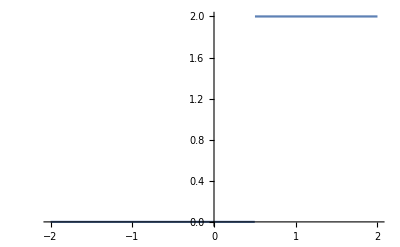

```mathematica
Plot[HeavisideTheta[-1/2+z]+HeavisideTheta[-1/2+z] ,{z,-2,2}]
```

```mathematica
f[k_,t_,z_]:=1/(2 k^2)√(π/2) (ⅇ^(-1/2 k (t+2 z)) (-ⅇ^(2 k z) HeavisideTheta[t-2 z]+ⅇ^(k t) (ⅇ^(2 k z) HeavisideTheta[-t/2-z]+HeavisideTheta[-t/2+z])-HeavisideTheta[t/2+z])+Sign[t-2 z]+Sign[t/2+z])
```

```mathematica
f2[k_,t_,z_]:=1/(2 k^2)√(π/2)(2HeavisideTheta[t/2-Abs[z]]-Exp[-k(t/2+z)]HeavisideTheta[t/2+z]-Exp[-k(t/2-z)]HeavisideTheta[t/2-z]+Exp[-k(-t/2-z)]HeavisideTheta[-t/2-z]+Exp[-k(-t/2+z)]HeavisideTheta[-t/2+z])
```

```mathematica
f3[k_,t_,z_]:=1/(2 k^2)√(π/2)(2(1-Cosh[k(t/2-Abs[z])])HeavisideTheta[t/2-Abs[z]]+Exp[k(t/2-Abs[z])])
```

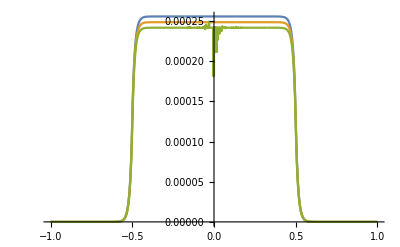

```mathematica
Plot[{f[70,1,z], f2[71,1,z], f3[72,1,z]},{z,-1,1},PlotPoints->50000]
```

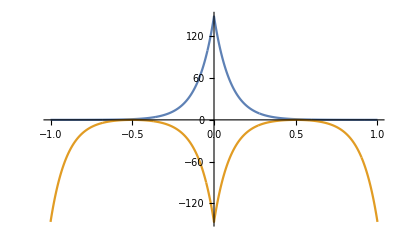

```mathematica
Plot[{Exp[10(1/2-Abs[z])],2(1-Cosh[10(1/2-Abs[z])])},{z,-1,1},PlotPoints->50000, PlotRange->Full]
```

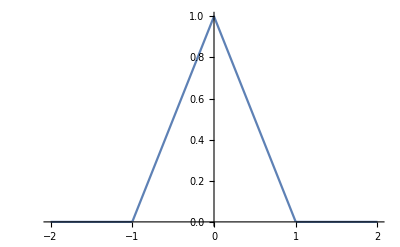

```mathematica
Plot[(2/2-Abs[z])HeavisideTheta[2/2-Abs[z]],{z,-2,2}, PlotRange->All]
```

```mathematica
FullSimplify[f[k,t,z]-f3[k,t,z]]
```

1/(2 k^2)√(π/2) (-ⅇ^(1/2 k (t-2 Abs[z]))+ⅇ^(-1/2 k (t+2 z)) (-ⅇ^(2 k z) HeavisideTheta[t-2 z]+ⅇ^(k t) (ⅇ^(2 k z) HeavisideTheta[-t/2-z]+HeavisideTheta[-t/2+z])-HeavisideTheta[t/2+z])+Sign[t-2 z]+Sign[t/2+z]+4 HeavisideTheta[t-2 Abs[z]] Sinh[1/4 k (t-2 Abs[z])]^2)

```mathematica
FullSimplify[f3[k,t,z],Assumptions->{k,t}>0&&z∈Reals]
```

(√(π/2) ((2-ⅇ^(-(k t)/2+k Abs[z])) HeavisideTheta[t-2 Abs[z]]+ⅇ^(1/2 k (t-2 Abs[z])) HeavisideTheta[-t/2+Abs[z]]))/(2 k^2)

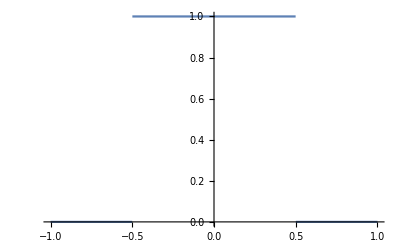

```mathematica
Plot[HeavisideTheta[1/2-Abs[z]], {z,-1,1}]
```

```mathematica
FullSimplify[%10]
```

1/(2 k^2)π (ⅇ^(-1/2 k (t+2 z)) (-ⅇ^(2 k z) HeavisideTheta[t-2 z]+ⅇ^(k t) (ⅇ^(2 k z) HeavisideTheta[-t/2-z]+HeavisideTheta[-t/2+z])-HeavisideTheta[t/2+z])+Sign[t-2 z]+Sign[t/2+z])

```mathematica
ExpToTrig[1/(2 k^2)π (ⅇ^(-1/2 k (t+2 z)) (-ⅇ^(2 k z) HeavisideTheta[t-2 z]+ⅇ^(k t) (ⅇ^(2 k z) HeavisideTheta[-t/2-z]+HeavisideTheta[-t/2+z])-HeavisideTheta[t/2+z])+Sign[t-2 z]+Sign[t/2+z])]
```

1/(2 k^2)π (Sign[t-2 z]+Sign[t/2+z]+(-Cosh[2 k z] HeavisideTheta[t-2 z]-HeavisideTheta[t/2+z]-HeavisideTheta[t-2 z] Sinh[2 k z]+(Cosh[k t]+Sinh[k t]) (Cosh[2 k z] HeavisideTheta[-t/2-z]+HeavisideTheta[-t/2+z]+HeavisideTheta[-t/2-z] Sinh[2 k z])) (Cosh[(k t)/2+k z]-Sinh[(k t)/2+k z]))

```mathematica
Simplify[%18]
```

1/(2 k^2)π (Sign[t-2 z]+Sign[t/2+z]+(-Cosh[2 k z] HeavisideTheta[t-2 z]-HeavisideTheta[t/2+z]-HeavisideTheta[t-2 z] Sinh[2 k z]+(Cosh[k t]+Sinh[k t]) (HeavisideTheta[-t/2+z]+HeavisideTheta[-t/2-z] (Cosh[2 k z]+Sinh[2 k z]))) (Cosh[1/2 k (t+2 z)]-Sinh[1/2 k (t+2 z)]))

```mathematica
TrigReduce[%19]
```

1/(2 k^2)(-π Cosh[2 k z-1/2 k (t+2 z)] HeavisideTheta[t-2 z]+π Cosh[k t+2 k z-1/2 k (t+2 z)] HeavisideTheta[-t/2-z]+π Cosh[k t-1/2 k (t+2 z)] HeavisideTheta[-t/2+z]-π Cosh[1/2 k (t+2 z)] HeavisideTheta[t/2+z]+π Sign[t-2 z]+π Sign[t/2+z]+π HeavisideTheta[t/2+z] Sinh[1/2 k (t+2 z)]+π HeavisideTheta[-t/2+z] Sinh[k t-1/2 k (t+2 z)]-π HeavisideTheta[t-2 z] Sinh[2 k z-1/2 k (t+2 z)]+π HeavisideTheta[-t/2-z] Sinh[k t+2 k z-1/2 k (t+2 z)])

```mathematica
FullSimplify[%20]
```

1/(2 k^2)π (ⅇ^(-1/2 k (t+2 z)) (-ⅇ^(2 k z) HeavisideTheta[t-2 z]+ⅇ^(k t) (ⅇ^(2 k z) HeavisideTheta[-t/2-z]+HeavisideTheta[-t/2+z])-HeavisideTheta[t/2+z])+Sign[t-2 z]+Sign[t/2+z])

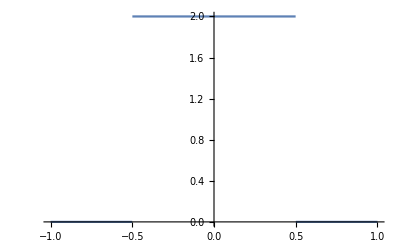

```mathematica
Plot[Sign[1-2 z]+Sign[1/2+z], {z,-1,1}]
```

```mathematica
1/(2 k^2)π (ⅇ^(k (π t+z)) HeavisideTheta[-π t-z]-ⅇ^(-k (π t+z)) (ⅇ^(2 k z) HeavisideTheta[π t-z]-ⅇ^(2 k π t) HeavisideTheta[-π t+z]+HeavisideTheta[π t+z])+Sign[π t-z]+Sign[π t+z])
```

```mathematica
1/(√(2π))Integrate[Exp[I kz z], {z,-t/2,t/2}, Assumptions->kz∈Reals&&t>0]
```

(√(2/π) Sin[(kz t)/2])/kz

```mathematica
Integrate[Exp[I 2π kz z], {z,-t/2,t/2}, Assumptions->kz∈Reals&&t>0]
```

Sin[kz π t]/(kz π)

```mathematica
Integrate[Exp[-I k ρ Cos[w+a]]Sin[w],{w,0,2π},Assumptions->Abs[a]<=π&&{k,ρ}≥0]
```

2 ⅈ π BesselJ[1,k ρ] Sin[a]

```mathematica
Integrate[Exp[-I k ρ Cos[w+a]]Cos[w],{w,0,2π},Assumptions->a<0&&{k,ρ}≥0]
```

-2 ⅈ π BesselJ[1,k ρ] Cos[a]

```mathematica
Integrate[k BesselK[0,k]BesselJ[1,k ρ]Exp[-k*z],{k,0,Infinity}]
```

∫_0^∞ ⅇ^(-k z) k BesselJ[1,k ρ] BesselK[0,k]ⅆk

```mathematica
∫_0^∞ ⅇ^(-k z) BesselJ[0,k ρ] BesselK[0,k]ⅆk
```

∫_0^∞ ⅇ^(-k z) BesselJ[0,k ρ] BesselK[0,k]ⅆk

```mathematica
Integrate[k Cos[k τ]Cos[ν-k ρ Sin[ν]]Exp[k(t/2-z)],{k,0,Infinity},Assumptions->{k,ρ,τ,ν,z}≥0&&t>0]
```

ConditionalExpression[Cos[ν]/(2 Abs[τ-ρ Sin[ν]]^2)+Cos[ν]/(2 Abs[τ+ρ Sin[ν]]^2)-Cos[ν]/(2 (τ-ρ Sin[ν])^2)-Cos[ν]/(2 (τ+ρ Sin[ν])^2)-(2 Sin[ν] (τ-ρ Sin[ν]) Sin[2 ArcTan[(2 Abs[τ-ρ Sin[ν]])/(-t+2 z)]])/(√((τ-ρ Sin[ν])^2) (t^2-4 t z+4 z^2+4 τ^2-8 ρ τ Sin[ν]+4 ρ^2 Sin[ν]^2))+(2 Cos[ν] (t Cos[3 ArcTan[(2 Abs[τ-ρ Sin[ν]])/(-t+2 z)]]-2 z Cos[3 ArcTan[(2 Abs[τ-ρ Sin[ν]])/(-t+2 z)]]-2 Abs[τ-ρ Sin[ν]] Sin[3 ArcTan[(2 Abs[τ-ρ Sin[ν]])/(-t+2 z)]]))/((t-2 z) (t^2-4 t z+4 z^2+4 τ^2-8 ρ τ Sin[ν]+4 ρ^2 Sin[ν]^2) √((t^2-4 t z+4 z^2+4 τ^2-8 ρ τ Sin[ν]+4 ρ^2 Sin[ν]^2)/(t-2 z)^2))+(2 Sin[ν] (τ+ρ Sin[ν]) Sin[2 ArcTan[(2 Abs[τ+ρ Sin[ν]])/(-t+2 z)]])/(√((τ+ρ Sin[ν])^2) (t^2-4 t z+4 z^2+4 τ^2+8 ρ τ Sin[ν]+4 ρ^2 Sin[ν]^2))+(2 Cos[ν] (t Cos[3 ArcTan[(2 Abs[τ+ρ Sin[ν]])/(-t+2 z)]]-2 z Cos[3 ArcTan[(2 Abs[τ+ρ Sin[ν]])/(-t+2 z)]]-2 Abs[τ+ρ Sin[ν]] Sin[3 ArcTan[(2 Abs[τ+ρ Sin[ν]])/(-t+2 z)]]))/((t-2 z) (t^2-4 t z+4 z^2+4 τ^2+8 ρ τ Sin[ν]+4 ρ^2 Sin[ν]^2) √((t^2-4 t z+4 z^2+4 τ^2+8 ρ τ Sin[ν]+4 ρ^2 Sin[ν]^2)/(t-2 z)^2)),t<2 z&&z>0]

```mathematica
Integrate[ BesselK[0,k]BesselJ[1,k ρ],{k,0,Infinity},Assumptions->ρ≥0]
```

ConditionalExpression[Log[1+ρ^2]/(2 ρ),ρ>0]

```mathematica
Limit[Log[1+ρ^2]/(2 ρ),ρ->0]
```

0

```mathematica
Integrate[ BesselK[0,k]BesselJ[1,k ρ](-k )^n,{k,0,Infinity},Assumptions->ρ≥0&&n>0&&n∈Integers]
```

ConditionalExpression[(-1)^n 2^(-1+n) ρ Gamma[1+n/2]^2 Hypergeometric2F1[(2+n)/2,(2+n)/2,2,-ρ^2],ρ>0]

```mathematica
FullSimplify[Hypergeometric2F1[(2+Abs[n])/2,(2+Abs[n])/2,2,-7^2], Assumptions->n∈Integers]
```

Hypergeometric2F1[1/2 (2+Abs[n]),1/2 (2+Abs[n]),2,-49]

```mathematica
∑_(n=0)^∞ ω^n/(n!)(-1)^n 2^(-1+n) ρ Gamma[1+n/2]^2 Hypergeometric2F1[(2+n)/2,(2+n)/2,2,-ρ^2]
```

∑_(n=0)^∞ ((-1)^n 2^(-1+n) ρ ω^n Gamma[1+n/2]^2 Hypergeometric2F1[(2+n)/2,(2+n)/2,2,-ρ^2])/(n!)

```mathematica
Integrate[ BesselK[0,k]((k ρ)/2)^(2n+1)Exp[-k ω],{k,0,Infinity},Assumptions->{ρ,ω}≥0&&n>0&&n∈Integers]
```

1/(4 (1+n)^2 ω)ρ^(1+2 n) (2 (1+n)^2 ω Gamma[1+n]^2 Hypergeometric2F1[1+n,1+n,1/2,ω^2]+Gamma[3/2+n]^2 (-(-1+ω^2) Hypergeometric2F1[3/2+n,3/2+n,-1/2,ω^2]+(-1+(6+4 n) ω^2) Hypergeometric2F1[3/2+n,3/2+n,1/2,ω^2]))

```mathematica
Simplify[%27]
```

1/(4 (1+n)^2 ω)ρ^(1+2 n) (2 (1+n)^2 ω Gamma[1+n]^2 Hypergeometric2F1[1+n,1+n,1/2,ω^2]+Gamma[3/2+n]^2 (-(-1+ω^2) Hypergeometric2F1[3/2+n,3/2+n,-1/2,ω^2]+(-1+(6+4 n) ω^2) Hypergeometric2F1[3/2+n,3/2+n,1/2,ω^2]))

```mathematica
Sum[Binomial[(3n)/2,n]Binomial[(3n)/2,n]((-ρ^2)^n)/(n+1),{n,0,Infinity}]
```

1/8 (8 HypergeometricPFQ[{1/3,1/3,2/3,2/3},{1/2,1,3/2},(729 ρ^4)/16]-9 ρ^2 HypergeometricPFQ[{5/6,5/6,7/6,7/6},{3/2,3/2,2},(729 ρ^4)/16])

```mathematica
Simplify[1/8 (8 HypergeometricPFQ[{1/3,1/3,2/3,2/3},{1/2,1,3/2},(729 ρ^4)/16]-9 ρ^2 HypergeometricPFQ[{5/6,5/6,7/6,7/6},{3/2,3/2,2},(729 ρ^4)/16])]
```

HypergeometricPFQ[{1/3,1/3,2/3,2/3},{1/2,1,3/2},(729 ρ^4)/16]-9/8 ρ^2 HypergeometricPFQ[{5/6,5/6,7/6,7/6},{3/2,3/2,2},(729 ρ^4)/16]

```mathematica
Simplify[1/4 (4 HypergeometricPFQ[{1/3,1/3,2/3,2/3},{1/2,1/2,1},(729 ρ^4)/16]-9 ρ^2 HypergeometricPFQ[{5/6,5/6,7/6,7/6},{1,3/2,3/2},(729 ρ^4)/16])]
```

HypergeometricPFQ[{1/3,1/3,2/3,2/3},{1/2,1/2,1},(729 ρ^4)/16]-9/4 ρ^2 HypergeometricPFQ[{5/6,5/6,7/6,7/6},{1,3/2,3/2},(729 ρ^4)/16]

```mathematica
Integrate[ BesselK[0,k]BesselJ[1,k ρ]Exp[-k ω],{k,0,Infinity},Assumptions->{ρ,ω}≥0]
```

Integrate[ⅇ^(-k ω) BesselJ[1,k ρ] BesselK[0,k],{k,0,∞},Assumptions→{ρ,ω}≥0]

```mathematica
Integrate[ BesselK[0,k]BesselJ[1,k ρ]Exp[-k ω]k,{k,0,Infinity},Assumptions->{ρ,ω}≥0]
```

Integrate[ⅇ^(-k ω) k BesselJ[1,k ρ] BesselK[0,k],{k,0,∞},Assumptions→{ρ,ω}≥0]

```mathematica
BesselK[0,k]
```

BesselK[0,k]

```mathematica
GeneratingFunction[BesselK[0,k],k,x]
```

GeneratingFunction::infy: Infinite expression 1/0 encountered.

GeneratingFunction[BesselK[0,k],k,x]

```mathematica
Integrate[ BesselJ[1,k ρ]Exp[-k ω]Exp[-k ρ Cosh[τ]],{k,0,Infinity},Assumptions->{ρ,ω,τ}≥0]
```

(1-1/(√(1+ρ^2/(ω+ρ Cosh[τ])^2)))/ρ

```mathematica
Simplify[(1-1/(√(1+ρ^2/(ω+ρ Cosh[τ])^2)))/ρ]
```

(1-1/(√(1+ρ^2/(ω+ρ Cosh[τ])^2)))/ρ

```mathematica
Cancel[(1-1/(√(1+ρ^2/(ω+ρ Cosh[τ])^2)))/ρ]
```

(-1+√(1+ρ^2/(ω+ρ Cosh[τ])^2))/(ρ √(1+ρ^2/(ω+ρ Cosh[τ])^2))

```mathematica
FullSimplify[(-1+√(1+ρ^2/(ω+ρ Cosh[τ])^2))/(ρ √(1+ρ^2/(ω+ρ Cosh[τ])^2))]
```

(1-1/(√(1+ρ^2/(ω+ρ Cosh[τ])^2)))/ρ

```mathematica
Integrate[(1-1/(√(1+ρ^2/(ω+ρ Cosh[τ])^2)))/ρ,{τ,0,Infinity},Assumptions->{ρ,ω}≥0]
```

Integrate[(1-1/(√(1+ρ^2/(ω+ρ Cosh[τ])^2)))/ρ,{τ,0,∞},Assumptions→{ρ,ω}≥0]

```mathematica
FullSimplify[(1-Ω/(√(ρ^2+Ω^2)))/ρ]
```

(1-Ω/(√(ρ^2+Ω^2)))/ρ

```mathematica
Cancel[(1-Ω/(√(ρ^2+Ω^2)))/ρ]
```

(-Ω+√(ρ^2+Ω^2))/(ρ √(ρ^2+Ω^2))

```mathematica
Simplify[(-Ω+√(ρ^2+Ω^2))/(ρ √(ρ^2+Ω^2))]
```

(1-Ω/(√(ρ^2+Ω^2)))/ρ

```mathematica
Cancel[(1-Ω/(√(ρ^2+Ω^2)))/ρ]
```

```mathematica
FullSimplify[-Ω/(√(ρ^2+Ω^2))]
```

```mathematica
-(Ω √(ρ^2+Ω^2))/(ρ^2+Ω^2)
```

-Ω/(√(ρ^2+Ω^2))

```mathematica
Integrate[ArcCos[ω-I ρ Sin[τ]]/(√(1-(ω-I ρ Sin[τ])^2)),τ,Assumptions->{ω,ρ}≥0]
```

Integrate[ArcCos[ω-ⅈ ρ Sin[τ]]/(√(1-(ω-ⅈ ρ Sin[τ])^2)),τ,Assumptions→{ω,ρ}≥0]

```mathematica
Simplify[%16]
```

(4 √2 EllipticF[ArcSin[√((((ⅈ ρ+√(-ρ^2-(-1+ω)^2))/(-1+ω)-(ⅈ ρ+√(-ρ^2-(1+ω)^2))/(1+ω)) (-ⅈ ρ+√(-ρ^2-(1+ω)^2)+(1+ω) Tan[τ/2]))/((1+ω) ((ⅈ ρ+√(-ρ^2-(-1+ω)^2))/(-1+ω)+(-ⅈ ρ+√(-ρ^2-(1+ω)^2))/(1+ω)) (-(ⅈ ρ+√(-ρ^2-(1+ω)^2))/(1+ω)+Tan[τ/2])))],(-1+ρ^2+ω^2-√(-ρ^2-(-1+ω)^2) √(-ρ^2-(1+ω)^2))/(-1+ρ^2+ω^2+√(-ρ^2-(-1+ω)^2) √(-ρ^2-(1+ω)^2))] (-(ⅈ ρ+√(-ρ^2-(-1+ω)^2)) Cos[τ/2]+(-1+ω) Sin[τ/2]) ((ρ-ⅈ √(-ρ^2-(1+ω)^2)) Cos[τ/2]+ⅈ (1+ω) Sin[τ/2]) √(((1+ω) √(-ρ^2-(1+ω)^2) (-ⅈ ρ+√(-ρ^2-(-1+ω)^2)+(-1+ω) Tan[τ/2]))/((-2 ⅈ ρ+√(-ρ^2-(-1+ω)^2)+√(-ρ^2-(-1+ω)^2) ω+√(-ρ^2-(1+ω)^2)-ω √(-ρ^2-(1+ω)^2)) (ⅈ ρ+√(-ρ^2-(1+ω)^2)-(1+ω) Tan[τ/2]))) √((((ⅈ ρ+√(-ρ^2-(-1+ω)^2))/(-1+ω)-(ⅈ ρ+√(-ρ^2-(1+ω)^2))/(1+ω)) (-ⅈ ρ+√(-ρ^2-(1+ω)^2)+(1+ω) Tan[τ/2]))/((1+ω) ((ⅈ ρ+√(-ρ^2-(-1+ω)^2))/(-1+ω)+(-ⅈ ρ+√(-ρ^2-(1+ω)^2))/(1+ω)) (-(ⅈ ρ+√(-ρ^2-(1+ω)^2))/(1+ω)+Tan[τ/2]))))/((2 ρ+ⅈ (-√(-ρ^2-(-1+ω)^2)-√(-ρ^2-(-1+ω)^2) ω-√(-ρ^2-(1+ω)^2)+ω √(-ρ^2-(1+ω)^2))) √(2+ρ^2-2 ω^2-ρ^2 Cos[2 τ]+4 ⅈ ρ ω Sin[τ]) √(-((1+ω) √(-ρ^2-(1+ω)^2) (-ⅈ ρ-√(-ρ^2-(-1+ω)^2)+(-1+ω) Tan[τ/2]))/((2 ⅈ ρ+√(-ρ^2-(-1+ω)^2)+√(-ρ^2-(-1+ω)^2) ω-√(-ρ^2-(1+ω)^2)+ω √(-ρ^2-(1+ω)^2)) (ⅈ ρ+√(-ρ^2-(1+ω)^2)-(1+ω) Tan[τ/2]))))

```mathematica
D[ArcCos[ω-I ρ Sin[τ]]/(√(1-(ω-I ρ Sin[τ])^2)),τ]
```

-(ⅈ ρ ArcCos[ω-ⅈ ρ Sin[τ]] Cos[τ] (ω-ⅈ ρ Sin[τ]))/((1-(ω-ⅈ ρ Sin[τ])^2)^(3/2))+(ⅈ ρ Cos[τ])/(1-(ω-ⅈ ρ Sin[τ])^2)

```mathematica
u[ω_,ρ_,τ_]:=ArcCos[ω-I ρ Sin[τ]]/(√(1-(ω-I ρ Sin[τ])^2))
```

```mathematica
FullSimplify[u[ω,ρ,π]-u[ω,ρ,-π]]
```

0

```mathematica
FullSimplify[-(ⅈ ρ ArcCos[ω-ⅈ ρ Sin[τ]] Cos[τ] (ω-ⅈ ρ Sin[τ]))/((1-(ω-ⅈ ρ Sin[τ])^2)^(3/2))+(ⅈ ρ Cos[τ])/(1-(ω-ⅈ ρ Sin[τ])^2)]
```

-ⅈ ρ Cos[τ] ((ArcCos[ω-ⅈ ρ Sin[τ]] (ω-ⅈ ρ Sin[τ]))/((1-(ω-ⅈ ρ Sin[τ])^2)^(3/2))-1/(1-(ω-ⅈ ρ Sin[τ])^2))

```mathematica
Integrate[Exp[I(τ-k ρ Cos[τ])],{τ,0,2π}]
```

ConditionalExpression[-2 ⅈ π BesselJ[1,k ρ],k ρ∈Reals]

```mathematica
Sin[ArcTan[x/d]]
```

x/(d √(1+x^2/d^2))

```mathematica
Manipulate[Plot[x/(d √(1+x^2/d^2)),{x,-1.2863733215943343,1.2863733215943343}],{d,-2.7371708245126283,2.7371708245126283}]
```

```mathematica
Cos[Tanh[x/d]]
```

Cos[Tanh[x/d]]

```mathematica
TrigToExp[Cos[Tanh[x/d]]]
```

1/2 ⅇ^(-(ⅈ (-ⅇ^(-x/d)+ⅇ^(x/d)))/(ⅇ^(-x/d)+ⅇ^(x/d)))+1/2 ⅇ^((ⅈ (-ⅇ^(-x/d)+ⅇ^(x/d)))/(ⅇ^(-x/d)+ⅇ^(x/d)))

```mathematica
ExpToTrig[1/2 ⅇ^(-(ⅈ (-ⅇ^(-x/d)+ⅇ^(x/d)))/(ⅇ^(-x/d)+ⅇ^(x/d)))+1/2 ⅇ^((ⅈ (-ⅇ^(-x/d)+ⅇ^(x/d)))/(ⅇ^(-x/d)+ⅇ^(x/d)))]
```

Cos[Tanh[x/d]]

```mathematica
Manipulate[Plot[Cos[Tanh[x/d]],{x,-8,8}],{d,-8,8}]
```

```mathematica
Manipulate[Plot[1/(√(1+x^2/d^2)),{x,-5,5}, PlotRange->{-0.5,1.1}],{d,0.00001,10}]
```